

```mathematica
Plot[x,{x,-2,2}]
```

```mathematica
Solve[√2==p/q,p]
```

{{p→√2 q}}

```mathematica
ApplySides[Function[x,x^2],√2==p/q]
```

2==p^2/q^2

```mathematica
Solve[2==p^2/q^2,p^2]
```

Solve::ivar: p^2 is not a valid variable.

Solve[2==p^2/q^2,p^2]

```mathematica
2 q^2==p^2
```

2 q^2==p^2

```mathematica
(2k)^2
```

4 k^2

```mathematica
Factor[(2k)^2]
```

4 k^2

```mathematica
FactorInteger[4]
```

{{2,2}}

```mathematica
2(2 k^2)
```

4 k^2

```mathematica
e==2eo
```

e==2 eo

```mathematica
Abs[x]
```

Abs[x]

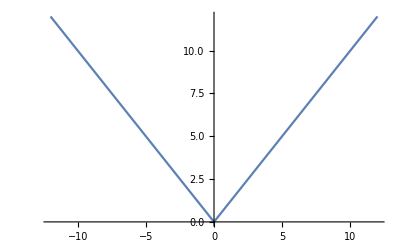

```mathematica
Plot[Abs[x],{x,-12.,12.}]
```

```mathematica
√(x^2)
```

√(x^2)

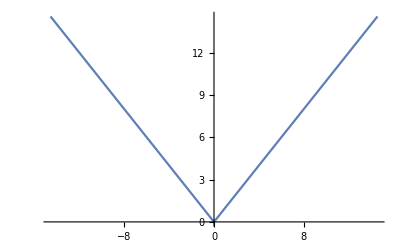

```mathematica
Plot[√(x^2),{x,-14.56,14.56}]
```

```mathematica
Simplify@√(x^2)
```

√(x^2)

```mathematica
FullSimplify[√(x^2),x∈Reals]
```

Abs[x]

```mathematica
FunctionRange[√(x^2),x,Reals]
```

ℝ≥0

```mathematica
FunctionRange[x^2,x,Reals]
```

ℝ≥0

```mathematica
√(x^2+1)
```

√(1+x^2)

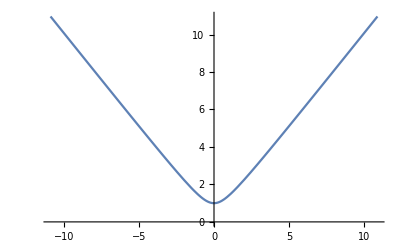

```mathematica
Plot[√(1+x^2),{x,-10.92,10.92}]
```

```mathematica
√(1+x^2)-x^2
```

-x^2+√(1+x^2)

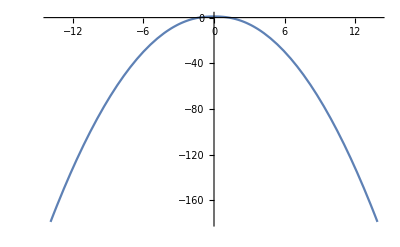

```mathematica
Plot[-x^2+√(1+x^2),{x,-13.890454572693635,13.890454572693635}]
```

```mathematica
Table[i^Subscript[a, i],{i,1,9}]
```

{1,2^a_2,3^a_3,4^a_4,5^a_5,6^a_6,7^a_7,8^a_8,9^a_9}

```mathematica
Total@{1,2^Subscript[a, 2],3^Subscript[a, 3],4^Subscript[a, 4],5^Subscript[a, 5],6^Subscript[a, 6],7^Subscript[a, 7],8^Subscript[a, 8],9^Subscript[a, 9]}
```

1+2^a_2+3^a_3+4^a_4+5^a_5+6^a_6+7^a_7+8^a_8+9^a_9

```mathematica
a∧b<->c
```

a&&b<->c

```mathematica
a∧b<->c ∧{a,b,c}∈Booleans
```

a&&b<->c&&(a|b|c)∈Booleans

```mathematica
True<->True
```

True<->True

```mathematica
a∨b==c
```

a||b==c

```mathematica
a∨a
```

a||a

```mathematica
LogicalExpand[a||a]
```

a

```mathematica
LogicalExpand[a||True]
```

True

```mathematica
ApplySides[ a&&# &,a||b==c]
```

ApplySides::eqin: a should be an equation or an inequality.

ApplySides[a&&#1&,a||b==c]

```mathematica
(a&&a)||b==(a&&c)
```

(a&&a)||b==(a&&c)

```mathematica
LogicalExpand[a&&a]
```

a

```mathematica
LogicalExpand[Not[a]&&a]
```

False

```mathematica
(Not[a]&&a)||b==(Not[a]&&c)
```

(!a&&a)||b==(!a&&c)

```mathematica
LogicalExpand[(!a&&a)||b]
```

b

```mathematica
LogicalExpand[(Not[a]&&a)||b==(Not[a]&&c)]
```

(!a&&c)==b

```mathematica
FindInstance[(!a&&c)==b,{a,b,c}]
```

FindInstance::nsmet: The methods available to FindInstance are insufficient to find the requested instances or prove they do not exist.

FindInstance[(!a&&c)==b,{a,b,c}]

```mathematica
FindInstance[(!a&&c)==b,{a,b,c},Booleans]
```

{{a→True,b→False,c→True}}

```mathematica
a&&((!a&&a)||b)==(a&&(!a&&c))
```

a&&((!a&&a)||b)==(a&&!a&&c)

```mathematica
LogicalExpand[a&&((!a&&a)||b)]
```

a&&b

```mathematica
LogicalExpand[(a&&!a&&c)]
```

False

```mathematica
LogicalExpand[(a&&(!a&&c))]
```

False

```mathematica
∏_(i=1)^n i
```

```mathematica
n!
```

n!

```mathematica
∑_(n=1)^∞ n!
```

Sum::div: Sum does not converge.

∑_(n=1)^∞ n!

```mathematica
n!+1
```

1+n!

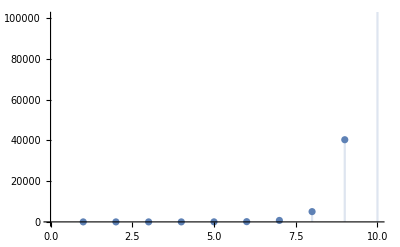

```mathematica
DiscretePlot[Gamma[n],{n,1,10}]
```

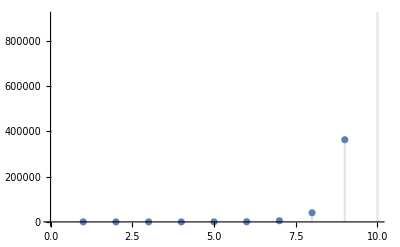

```mathematica
DiscretePlot[n!,{n,1,10}]
```

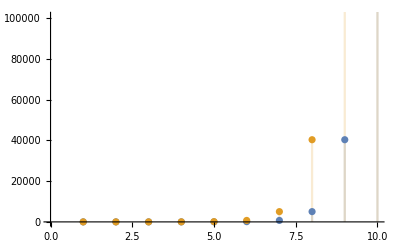

```mathematica
DiscretePlot[{Gamma[n],n!},{n,1,10}]
```

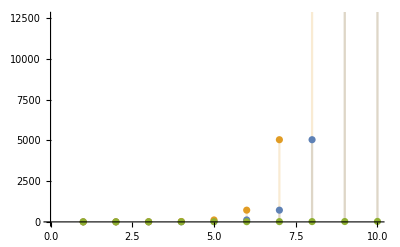

```mathematica
DiscretePlot[{Gamma[n],n!,Prime[n]},{n,1,10}]
```

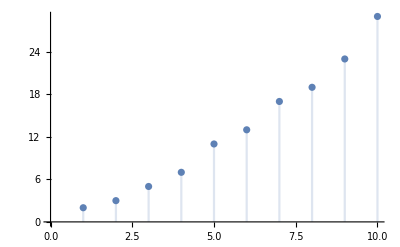

```mathematica
DiscretePlot[{Prime[n]},{n,1,10}]
```

```mathematica
Prime[0]
```

Prime::intpp: Positive integer argument expected in Prime[0].

Prime[0]

```mathematica
Prime[1]
```

2

```mathematica
Table[Prime[i],{i,1,100}]
```

{2,3,5,7,11,13,17,19,23,29,31,37,41,43,47,53,59,61,67,71,73,79,83,89,97,101,103,107,109,113,127,131,137,139,149,151,157,163,167,173,179,181,191,193,197,199,211,223,227,229,233,239,241,251,257,263,269,271,277,281,283,293,307,311,313,317,331,337,347,349,353,359,367,373,379,383,389,397,401,409,419,421,431,433,439,443,449,457,461,463,467,479,487,491,499,503,509,521,523,541}

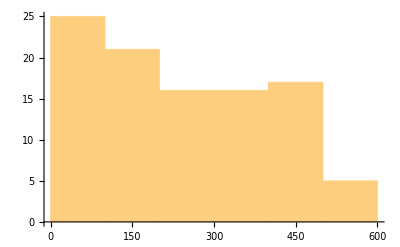

```mathematica
Histogram[%56]
```

```mathematica
Differences@Table[Prime[i],{i,1,100}]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18}

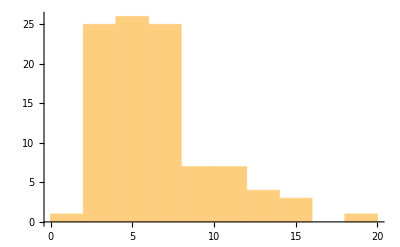

```mathematica
Histogram[%57]
```

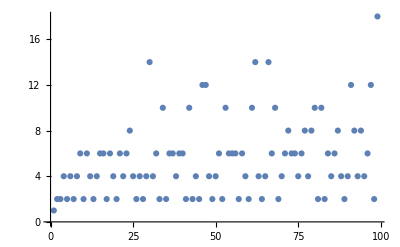

```mathematica
ListPlot[%57]
```

```mathematica
Total[%57]
```

539

```mathematica
Differences@Table[Prime[i],{i,1,10000}]
```

{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18,6,10,6,6,2,6,10,6,6,2,6,6,4,2,12,10,2,4,6,6,2,12,4,6,8,10,8,10,8,6,6,4,8,6,4,8,4,14,10,12,2,10,2,4,2,10,14,4,2,4,14,4,2,4,20,4,8,10,8,4,6,6,14,4,6,6,8,6,12,4,6,2,10,2,6,10,2,10,2,6,18,4,2,4,6,6,8,6,6,22,2,10,8,10,6,6,8,12,4,6,6,2,6,12,10,18,2,4,6,2,6,4,2,4,12,2,6,34,6,6,8,18,10,14,4,2,4,6,8,4,2,6,12,10,2,4,2,4,6,12,12,8,12,6,4,6,8,4,8,4,14,4,6,2,4,6,2,6,10,20,6,4,2,24,4,2,10,12,2,10,8,6,6,6,18,6,4,2,12,10,12,8,16,14,6,4,2,4,2,10,12,6,6,18,2,16,2,22,6,8,6,4,2,4,8,6,10,2,10,14,10,6,12,2,4,2,10,12,2,16,2,6,4,2,10,8,18,24,4,6,8,16,2,4,8,16,2,4,8,6,6,4,12,2,22,6,2,6,4,6,14,6,4,2,6,4,6,12,6,6,14,4,6,12,8,6,4,26,18,10,8,4,6,2,6,22,12,2,16,8,4,12,14,10,2,4,8,6,6,4,2,4,6,8,4,2,6,10,2,10,8,4,14,10,12,2,6,4,2,16,14,4,6,8,6,4,18,8,10,6,6,8,10,12,14,4,6,6,2,28,2,10,8,4,14,4,8,12,6,12,4,6,20,10,2,16,26,4,2,12,6,4,12,6,8,4,8,22,2,4,2,12,28,2,6,6,6,4,6,2,12,4,12,2,10,2,16,2,16,6,20,16,8,4,2,4,2,22,8,12,6,10,2,4,6,2,6,10,2,12,10,2,10,14,6,4,6,8,6,6,16,12,2,4,14,6,4,8,10,8,6,6,22,6,2,10,14,4,6,18,2,10,14,4,2,10,14,4,8,18,4,6,2,4,6,2,12,4,20,22,12,2,4,6,6,2,6,22,2,6,16,6,12,2,6,12,16,2,4,6,14,4,2,18,24,10,6,2,10,2,10,2,10,6,2,10,2,10,6,8,30,10,2,10,8,6,10,18,6,12,12,2,18,6,4,6,6,18,2,10,14,6,4,2,4,24,2,12,6,16,8,6,6,18,16,2,4,6,2,6,6,10,6,12,12,18,2,6,4,18,8,24,4,2,4,6,2,12,4,14,30,10,6,12,14,6,10,12,2,4,6,8,6,10,2,4,14,6,6,4,6,2,10,2,16,12,8,18,4,6,12,2,6,6,6,28,6,14,4,8,10,8,12,18,4,2,4,24,12,6,2,16,6,6,14,10,14,4,30,6,6,6,8,6,4,2,12,6,4,2,6,22,6,2,4,18,2,4,12,2,6,4,26,6,6,4,8,10,32,16,2,6,4,2,4,2,10,14,6,4,8,10,6,20,4,2,6,30,4,8,10,6,6,8,6,12,4,6,2,6,4,6,2,10,2,16,6,20,4,12,14,28,6,20,4,18,8,6,4,6,14,6,6,10,2,10,12,8,10,2,10,8,12,10,24,2,4,8,6,4,8,18,10,6,6,2,6,10,12,2,10,6,6,6,8,6,10,6,2,6,6,6,10,8,24,6,22,2,18,4,8,10,30,8,18,4,2,10,6,2,6,4,18,8,12,18,16,6,2,12,6,10,2,10,2,6,10,14,4,24,2,16,2,10,2,10,20,4,2,4,8,16,6,6,2,12,16,8,4,6,30,2,10,2,6,4,6,6,8,6,4,12,6,8,12,4,14,12,10,24,6,12,6,2,22,8,18,10,6,14,4,2,6,10,8,6,4,6,30,14,10,2,12,10,2,16,2,18,24,18,6,16,18,6,2,18,4,6,2,10,8,10,6,6,8,4,6,2,10,2,12,4,6,6,2,12,4,14,18,4,6,20,4,8,6,4,8,4,14,6,4,14,12,4,2,30,4,24,6,6,12,12,14,6,4,2,4,18,6,12,8,6,4,12,2,12,30,16,2,6,22,14,6,10,12,6,2,4,8,10,6,6,24,14,6,4,8,12,18,10,2,10,2,4,6,20,6,4,14,4,2,4,14,6,12,24,10,6,8,10,2,30,4,6,2,12,4,14,6,34,12,8,6,10,2,4,20,10,8,16,2,10,14,4,2,12,6,16,6,8,4,8,4,6,8,6,6,12,6,4,6,6,8,18,4,20,4,12,2,10,6,2,10,12,2,4,20,6,30,6,4,8,10,12,6,2,28,2,6,4,2,16,12,2,6,10,8,24,12,6,18,6,4,14,6,4,12,8,6,12,4,6,12,6,12,2,16,20,4,2,10,18,8,4,14,4,2,6,22,6,14,6,6,10,6,2,10,2,4,2,22,2,4,6,6,12,6,14,10,12,6,8,4,36,14,12,6,4,6,2,12,6,12,16,2,10,8,22,2,12,6,4,6,18,2,12,6,4,12,8,6,12,4,6,12,6,2,12,12,4,14,6,16,6,2,10,8,18,6,34,2,28,2,22,6,2,10,12,2,6,4,8,22,6,2,10,8,4,6,8,4,12,18,12,20,4,6,6,8,4,2,16,12,2,10,8,10,2,4,6,14,12,22,8,28,2,4,20,4,2,4,14,10,12,2,12,16,2,28,8,22,8,4,6,6,14,4,8,12,6,6,4,20,4,18,2,12,6,4,6,14,18,10,8,10,32,6,10,6,6,2,6,16,6,2,12,6,28,2,10,8,16,6,8,6,10,24,20,10,2,10,2,12,4,6,20,4,2,12,18,10,2,10,2,4,20,16,26,4,8,6,4,12,6,8,12,12,6,4,8,22,2,16,14,10,6,12,12,14,6,4,20,4,12,6,2,6,6,16,8,22,2,28,8,6,4,20,4,12,24,20,4,8,10,2,16,2,12,12,34,2,4,6,12,6,6,8,6,4,2,6,24,4,20,10,6,6,14,4,6,6,2,12,6,10,2,10,6,20,4,26,4,2,6,22,2,24,4,6,2,4,6,24,6,8,4,2,34,6,8,16,12,2,10,2,10,6,8,4,8,12,22,6,14,4,26,4,2,12,10,8,4,8,12,4,14,6,16,6,8,4,6,6,8,6,10,12,2,6,6,16,8,6,6,12,10,2,6,18,4,6,6,6,12,18,8,6,10,8,18,4,14,6,18,10,8,10,12,2,6,12,12,36,4,6,8,4,6,2,4,18,12,6,8,6,6,4,18,2,4,2,24,4,6,6,14,30,6,4,6,12,6,20,4,8,4,8,6,6,4,30,2,10,12,8,10,8,24,6,12,4,14,4,6,2,28,14,16,2,12,6,4,20,10,6,6,6,8,10,12,14,10,14,16,14,10,14,6,16,6,8,6,16,20,10,2,6,4,2,4,12,2,10,2,6,22,6,2,4,18,8,10,8,22,2,10,18,14,4,2,4,18,2,4,6,8,10,2,30,4,30,2,10,2,18,4,18,6,14,10,2,4,20,36,6,4,6,14,4,20,10,14,22,6,2,30,12,10,18,2,4,14,6,22,18,2,12,6,4,8,4,8,6,10,2,12,18,10,14,16,14,4,6,6,2,6,4,2,28,2,28,6,2,4,6,14,4,12,14,16,14,4,6,8,6,4,6,6,6,8,4,8,4,14,16,8,6,4,12,8,16,2,10,8,4,6,26,6,10,8,4,6,12,14,30,4,14,22,8,12,4,6,8,10,6,14,10,6,2,10,12,12,14,6,6,18,10,6,8,18,4,6,2,6,10,2,10,8,6,6,10,2,18,10,2,12,4,6,8,10,12,14,12,4,8,10,6,6,20,4,14,16,14,10,8,10,12,2,18,6,12,10,12,2,4,2,12,6,4,8,4,44,4,2,4,2,10,12,6,6,14,4,6,6,6,8,6,36,18,4,6,2,12,6,6,6,4,14,22,12,2,18,10,6,26,24,4,2,4,2,4,14,4,6,6,8,16,12,2,42,4,2,4,24,6,6,2,18,4,14,6,28,18,14,6,10,12,2,6,12,30,6,4,6,6,14,4,2,24,4,6,6,26,10,18,6,8,6,6,30,4,12,12,2,16,2,6,4,12,18,2,6,4,26,12,6,12,4,24,24,12,6,2,12,28,8,4,6,12,2,18,6,4,6,6,20,16,2,6,6,18,10,6,2,4,8,6,6,24,16,6,8,10,6,14,22,8,16,6,2,12,4,2,22,8,18,34,2,6,18,4,6,6,8,10,8,18,6,4,2,4,8,16,2,12,12,6,18,4,6,6,6,2,6,12,10,20,12,18,4,6,2,16,2,10,14,4,30,2,10,12,2,24,6,16,8,10,2,12,22,6,2,16,20,10,2,12,12,18,10,12,6,2,10,2,6,10,18,2,12,6,4,6,2,24,28,2,4,2,10,2,16,12,8,22,2,6,4,2,10,6,20,12,10,8,12,6,6,6,4,18,2,4,12,18,2,12,6,4,2,16,12,12,14,4,8,18,4,12,14,6,6,4,8,6,4,20,12,10,14,4,2,16,2,12,30,4,6,24,20,24,10,8,12,10,12,6,12,12,6,8,16,14,6,4,6,36,20,10,30,12,2,4,2,28,12,14,6,22,8,4,18,6,14,18,4,6,2,6,34,18,2,16,6,18,2,24,4,2,6,12,6,12,10,8,6,16,12,8,10,14,40,6,2,6,4,12,14,4,2,4,2,4,8,6,10,6,6,2,6,6,6,12,6,24,10,2,10,6,12,6,6,14,6,6,52,20,6,10,2,10,8,10,12,12,2,6,4,14,16,8,12,6,22,2,10,8,6,22,2,22,6,8,10,12,12,2,10,6,12,2,4,14,10,2,6,18,4,12,8,18,12,6,6,4,6,6,14,4,2,12,12,4,6,18,18,12,2,16,12,8,18,10,26,4,6,8,6,6,4,2,10,20,4,6,8,4,20,10,2,34,2,4,24,2,12,12,10,6,2,12,30,6,12,16,12,2,22,18,12,14,10,2,12,12,4,2,4,6,12,2,16,18,2,40,8,16,6,8,10,2,4,18,8,10,8,12,4,18,2,18,10,2,4,2,4,8,28,2,6,22,12,6,14,18,4,6,8,6,6,10,8,4,2,18,10,6,20,22,8,6,30,4,2,4,18,6,30,2,4,8,6,4,6,12,14,34,14,6,4,2,6,4,14,4,2,6,28,2,4,6,8,10,2,10,2,10,2,4,30,2,12,12,10,18,12,14,10,2,12,6,10,6,14,12,4,14,4,18,2,10,8,4,8,10,12,18,18,8,6,18,16,14,6,6,10,14,4,6,2,12,12,4,6,6,12,2,16,2,12,6,4,14,6,4,2,12,18,4,36,18,12,12,2,4,2,4,8,12,4,36,6,18,2,12,10,6,12,24,8,6,6,16,12,2,18,10,20,10,2,6,18,4,2,40,6,2,16,2,4,8,18,10,12,6,2,10,8,4,6,12,2,10,18,8,6,4,20,4,6,36,6,2,10,6,24,6,14,16,6,18,2,10,20,10,8,6,4,6,2,10,2,12,4,2,4,8,10,6,12,18,14,12,16,8,6,16,8,4,2,6,18,24,18,10,12,2,4,14,10,6,6,6,18,12,2,28,18,14,16,12,14,24,12,22,6,2,10,8,4,2,4,14,12,6,4,6,14,4,2,4,30,6,2,6,10,2,30,22,2,4,6,8,6,6,16,12,12,6,8,4,2,24,12,4,6,8,6,6,10,2,6,12,28,14,6,4,12,8,6,12,4,6,14,6,12,10,6,6,8,6,6,4,2,4,8,12,4,14,18,10,2,16,6,20,6,10,8,4,30,36,12,8,22,12,2,6,12,16,6,6,2,18,4,26,4,8,18,10,8,10,6,14,4,20,22,18,12,8,28,12,6,6,8,6,12,24,16,14,4,14,12,6,10,12,20,6,4,8,18,12,18,10,2,4,20,10,14,4,6,2,10,24,18,2,4,20,16,14,10,14,6,4,6,20,6,10,6,2,12,6,30,10,8,6,4,6,8,40,2,4,2,12,18,4,6,8,10,6,18,18,2,12,16,8,6,4,6,6,2,52,14,4,20,16,2,4,6,12,2,6,12,12,6,4,14,10,6,6,14,10,14,16,8,6,12,4,8,22,6,2,18,22,6,2,18,6,16,14,10,6,12,2,6,4,8,18,12,16,2,4,14,4,8,12,12,30,16,8,4,2,6,22,12,8,10,6,6,6,14,6,18,10,12,2,10,2,4,26,4,12,8,4,18,8,10,14,16,6,6,8,10,6,8,6,12,10,20,10,8,4,12,26,18,4,12,18,6,30,6,8,6,22,12,2,4,6,6,2,10,2,4,6,6,2,6,22,18,6,18,12,8,12,6,10,12,2,16,2,10,2,10,18,6,20,4,2,6,22,6,6,18,6,14,12,16,2,6,6,4,14,12,4,2,18,16,36,12,6,14,28,2,12,6,12,6,4,2,16,30,8,24,6,30,10,2,18,4,6,12,8,22,2,6,22,18,2,10,2,10,30,2,28,6,14,16,6,20,16,2,6,4,32,4,2,4,6,2,12,4,6,6,12,2,6,4,6,8,6,4,20,4,32,10,8,16,2,22,2,4,6,8,6,16,14,4,18,8,4,20,6,12,12,6,10,2,10,2,12,28,12,18,2,18,10,8,10,48,2,4,6,8,10,2,10,30,2,36,6,10,6,2,18,4,6,8,16,14,16,6,14,4,20,4,6,2,10,12,2,6,12,6,6,4,12,2,6,4,12,6,8,4,2,6,18,10,6,8,12,6,22,2,6,12,18,4,14,6,4,20,6,16,8,4,8,22,8,12,6,6,16,12,18,30,8,4,2,4,6,26,4,14,24,22,6,2,6,10,6,14,6,6,12,10,6,2,12,10,12,8,18,18,10,6,8,16,6,6,8,16,20,4,2,10,2,10,12,6,8,6,10,20,10,18,26,4,6,30,2,4,8,6,12,12,18,4,8,22,6,2,12,34,6,18,12,6,2,28,14,16,14,4,14,12,4,6,6,2,36,4,6,20,12,24,6,22,2,16,18,12,12,18,2,6,6,6,4,6,14,4,2,22,8,12,6,10,6,8,12,18,12,6,10,2,22,14,6,6,4,18,6,20,22,2,12,24,4,18,18,2,22,2,4,12,8,12,10,14,4,2,18,16,38,6,6,6,12,10,6,12,8,6,4,6,14,30,6,10,8,22,6,8,12,10,2,10,2,6,10,2,10,12,18,20,6,4,8,22,6,6,30,6,14,6,12,12,6,10,2,10,30,2,16,8,4,2,6,18,4,2,6,4,26,4,8,6,10,2,4,6,8,4,6,30,12,2,6,6,4,20,22,8,4,2,4,72,8,4,8,22,2,4,14,10,2,4,20,6,10,18,6,20,16,6,8,6,4,20,12,22,2,4,2,12,10,18,2,22,6,18,30,2,10,14,10,8,16,50,6,10,8,10,12,6,18,2,22,6,2,4,6,8,6,6,10,18,2,22,2,16,14,10,6,2,12,10,20,4,14,6,4,36,2,4,6,12,2,4,14,12,6,4,6,2,6,4,20,10,2,10,6,12,2,24,12,12,6,6,4,24,2,4,24,2,6,4,6,8,16,6,2,10,12,14,6,34,6,14,6,4,2,30,22,8,4,6,8,4,2,28,2,6,4,26,18,22,2,6,16,6,2,16,12,2,12,4,6,6,14,10,6,8,12,4,18,2,10,8,16,6,6,30,2,10,18,2,10,8,4,8,12,24,40,2,12,10,6,12,2,12,4,2,4,6,18,14,12,6,4,14,30,4,8,10,8,6,10,18,8,4,14,16,6,8,4,6,2,10,2,12,4,2,4,6,8,4,6,32,24,10,8,18,10,2,6,10,2,4,18,6,12,2,16,2,22,6,6,8,18,4,18,12,8,6,4,20,6,30,22,12,2,6,18,4,62,4,2,12,6,10,2,12,12,28,2,4,14,22,6,2,6,6,10,14,4,2,10,6,8,10,14,10,6,2,12,22,18,8,10,18,12,2,12,4,12,2,10,2,6,18,6,6,34,6,2,12,4,6,18,18,2,16,6,6,8,6,10,18,8,10,8,10,2,4,18,26,12,22,2,4,2,22,6,6,14,16,6,20,10,12,2,18,42,4,24,2,6,10,12,2,6,10,8,4,6,12,12,8,4,6,12,30,20,6,24,6,10,12,2,10,20,6,6,4,12,14,10,18,12,8,6,12,4,14,10,2,12,30,16,2,12,6,4,2,4,6,26,4,18,2,4,6,14,54,6,52,2,16,6,6,12,26,4,2,6,22,6,2,12,12,6,10,18,2,12,12,10,18,12,6,8,6,10,6,8,4,2,4,20,24,6,6,10,14,10,2,22,6,14,10,26,4,18,8,12,12,10,12,6,8,16,6,8,6,6,22,2,10,20,10,6,44,18,6,10,2,4,6,14,4,26,4,2,12,10,8,4,8,12,4,12,8,22,8,6,10,18,6,6,8,6,12,4,8,18,10,12,6,12,2,6,4,2,16,12,12,14,10,14,6,10,12,2,12,6,4,6,2,12,4,26,6,18,6,10,6,2,18,10,8,4,26,10,20,6,16,20,12,10,8,10,2,16,6,20,10,20,4,30,2,4,8,16,2,18,4,2,6,10,18,12,14,18,6,16,20,6,4,8,6,4,6,12,8,10,2,12,6,4,2,6,10,2,16,12,14,10,6,8,6,28,2,6,18,30,34,2,16,12,2,18,16,6,8,10,8,10,8,10,44,6,6,4,20,4,2,4,14,28,8,6,16,14,30,6,30,4,14,10,6,6,8,4,18,12,6,2,22,12,8,6,12,4,14,4,6,2,4,18,20,6,16,38,16,2,4,6,2,40,42,14,4,6,2,24,10,6,2,18,10,12,2,16,2,6,16,6,8,4,2,10,6,8,10,2,18,16,8,12,18,12,6,12,10,6,6,18,12,14,4,2,10,20,6,12,6,16,26,4,18,2,4,32,10,8,6,4,6,6,14,6,18,4,2,18,10,8,10,8,10,2,4,6,2,10,42,8,12,4,6,18,2,16,8,4,2,10,14,12,10,20,4,8,10,38,4,6,2,10,20,10,12,6,12,26,12,4,8,28,8,4,8,24,6,10,8,6,16,12,8,10,12,8,22,6,2,10,2,6,10,6,6,8,6,4,14,28,8,16,18,8,4,6,20,4,18,6,2,24,24,6,6,12,12,4,2,22,2,10,6,8,12,4,20,18,6,4,12,24,6,6,54,8,6,4,26,36,4,2,4,26,12,12,4,6,6,8,12,10,2,12,16,18,6,8,6,12,18,10,2,54,4,2,10,30,12,8,4,8,16,14,12,6,4,6,12,6,2,4,14,12,4,14,6,24,6,6,10,12,12,20,18,6,6,16,8,4,6,20,4,32,4,14,10,2,6,12,16,2,4,6,12,2,10,8,6,4,2,10,14,6,6,12,18,34,8,10,6,24,6,2,10,12,2,30,10,14,12,12,16,6,6,2,18,4,6,30,14,4,6,6,2,6,4,6,14,6,4,8,10,12,6,32,10,8,22,2,10,6,24,8,4,30,6,2,12,16,8,6,4,6,8,16,14,6,6,4,2,10,12,2,16,14,4,2,4,20,18,10,2,10,6,12,30,8,18,12,10,2,6,6,4,12,12,2,4,12,18,24,2,10,6,8,16,8,6,12,10,14,6,12,6,6,4,2,24,4,6,8,6,4,2,4,6,14,4,8,10,24,24,12,2,6,12,22,30,2,6,18,10,6,6,8,4,2,6,10,8,10,6,8,16,6,14,6,4,24,8,10,2,12,6,4,36,2,22,6,8,6,10,8,6,12,10,14,10,6,18,12,2,12,4,26,10,14,16,18,8,18,12,12,6,16,14,24,10,12,8,22,6,2,10,60,6,2,4,8,16,14,10,6,24,6,12,18,24,2,30,4,2,12,6,10,2,4,14,6,16,2,10,8,22,20,6,4,32,6,18,4,2,4,2,4,8,52,14,22,2,22,20,10,8,10,2,6,4,14,4,6,20,4,6,2,12,12,6,12,16,2,12,10,8,4,6,2,28,12,8,10,12,2,4,14,28,8,6,4,2,4,6,2,12,58,6,14,10,2,6,28,32,4,30,8,6,4,6,12,12,2,4,6,6,14,16,8,30,4,2,10,8,6,4,6,26,4,12,2,10,18,12,12,18,2,4,12,8,12,10,20,4,8,16,12,8,6,16,8,10,12,14,6,4,8,12,4,20,6,40,8,16,6,36,2,6,4,6,2,22,18,2,10,6,36,14,12,4,18,8,4,14,10,2,10,8,4,2,18,16,12,14,10,14,6,6,42,10,6,6,20,10,8,12,4,12,18,2,10,14,18,10,18,8,6,4,14,6,10,30,14,6,6,4,12,38,4,2,4,6,8,12,10,6,18,6,50,6,4,6,12,8,10,32,6,22,2,10,12,18,2,6,4,30,8,6,6,18,10,2,4,12,20,10,8,24,10,2,6,22,6,2,18,10,12,2,30,18,12,28,2,6,4,6,14,6,12,10,8,4,12,26,10,8,6,16,2,10,18,14,6,4,6,14,16,2,6,4,12,20,4,20,4,6,12,2,36,4,6,2,10,2,22,8,6,10,12,12,18,14,24,36,4,20,24,10,6,2,28,6,18,8,4,6,8,6,4,2,12,28,18,14,16,14,18,10,8,6,4,6,6,8,22,12,2,10,18,6,2,18,10,2,12,10,18,32,6,4,6,6,8,6,6,10,20,6,12,10,8,10,14,6,10,14,4,2,22,18,2,10,2,4,20,4,2,34,2,12,6,10,2,10,18,6,14,12,12,22,8,6,16,6,8,4,12,6,8,4,36,6,6,20,24,6,12,18,10,2,10,26,6,16,8,6,4,24,18,8,12,12,10,18,12,2,24,4,12,18,12,14,10,2,4,24,12,14,10,6,2,6,4,6,26,4,6,6,2,22,8,18,4,18,8,4,24,2,12,12,4,2,52,2,18,6,4,6,12,2,6,12,10,8,4,2,24,10,2,10,2,12,6,18,40,6,20,16,2,12,6,10,12,2,4,6,14,12,12,22,6,8,4,2,16,18,12,2,6,16,6,2,6,4,12,30,8,16,2,18,10,24,2,6,24,4,2,22,2,16,2,6,12,4,18,8,4,14,4,18,24,6,2,6,10,2,10,38,6,10,14,6,6,24,4,2,12,16,14,16,12,2,6,10,26,4,2,12,6,4,12,8,12,10,18,6,14,28,2,6,10,2,4,14,34,2,6,22,2,10,14,4,2,16,8,10,6,8,10,8,4,6,2,16,6,6,18,30,14,6,4,30,2,10,14,4,20,10,8,4,8,18,4,14,6,4,24,6,6,18,18,2,36,6,10,14,12,4,6,2,30,6,4,2,6,28,20,4,20,12,24,16,18,12,14,6,4,12,32,12,6,10,8,10,6,18,2,16,14,6,22,6,12,2,18,4,8,30,12,4,12,2,10,38,22,2,4,14,6,12,24,4,2,4,14,12,10,2,16,6,20,4,20,22,12,2,4,2,12,22,24,6,6,2,6,4,6,2,10,12,12,6,2,6,16,8,6,4,18,12,12,14,4,12,6,8,6,18,6,10,12,14,6,4,8,22,6,2,28,18,2,18,10,6,14,10,2,10,14,6,10,2,22,6,8,6,16,12,8,22,2,4,14,18,12,6,24,6,10,2,12,22,18,6,20,6,10,14,4,2,6,12,22,14,12,4,6,8,22,2,10,12,8,40,2,6,10,8,4,42,20,4,32,12,10,6,12,12,2,10,8,6,4,8,4,26,18,4,8,28,6,18,6,12,2,10,6,6,14,10,12,14,24,6,4,20,22,2,18,4,6,12,2,16,18,14,6,6,4,6,8,18,4,14,30,4,18,8,10,2,4,8,12,4,12,18,2,12,10,2,16,8,4,30,2,6,28,2,10,2,18,10,14,4,26,6,18,4,20,6,4,8,18,4,12,26,24,4,20,22,2,18,22,2,4,12,2,6,6,6,4,6,14,4,24,12,6,18,2,12,28,14,4,6,8,22,6,12,18,8,4,20,6,4,6,2,18,6,4,12,12,8,28,6,8,10,2,24,12,10,24,8,10,20,12,6,12,12,4,14,12,24,34,18,8,10,6,18,8,4,8,16,14,6,4,6,24,2,6,4,6,2,16,6,6,20,24,4,2,4,14,4,18,2,6,12,4,14,4,2,18,16,6,6,2,16,20,6,6,30,4,8,6,24,16,6,6,8,12,30,4,18,18,8,4,26,10,2,22,8,10,14,6,4,18,8,12,28,2,6,4,12,6,24,6,8,10,20,16,8,30,6,6,4,2,10,14,6,10,32,22,18,2,4,2,4,8,22,8,18,12,28,2,16,12,18,14,10,18,12,6,32,10,14,6,10,2,10,2,6,22,2,4,6,8,10,6,14,6,4,12,30,24,6,6,8,6,4,2,4,6,8,6,6,22,18,8,4,2,18,6,4,2,16,18,20,10,6,6,30,2,12,28,6,6,6,2,12,10,8,18,18,4,8,18,10,2,28,2,10,14,4,2,30,12,22,26,10,8,6,10,8,16,14,6,6,10,14,6,4,2,10,12,2,6,10,8,4,2,10,26,22,6,2,12,18,4,26,4,8,10,6,14,10,2,18,6,10,20,6,6,4,24,2,4,8,6,16,14,16,18,2,4,12,2,10,2,6,12,10,6,6,20,6,4,6,38,4,6,12,14,4,12,8,10,12,12,8,4,6,14,10,6,12,2,10,18,2,18,10,8,10,2,12,4,14,28,2,16,2,18,6,10,6,8,16,14,30,10,20,6,10,24,2,28,2,12,16,6,8,36,4,8,4,14,12,10,8,12,4,6,8,4,6,14,22,8,6,4,2,10,6,20,10,8,6,6,22,18,2,16,6,20,4,26,4,14,22,14,4,12,6,8,4,6,6,26,10,2,18,18,4,2,16,2,18,4,6,8,4,6,12,2,6,6,28,38,4,8,16,26,4,2,10,12,2,10,8,6,10,12,2,10,2,24,4,30,26,6,6,18,6,6,22,2,10,18,26,4,18,8,6,6,12,16,6,8,16,6,8,16,2,42,58,8,4,6,2,4,8,16,6,20,4,12,12,6,12,2,10,2,6,22,2,10,6,8,6,10,14,6,6,4,18,8,10,8,16,14,10,2,10,2,12,6,4,20,10,8,52,8,10,6,2,10,8,10,6,6,8,10,2,22,2,4,6,14,4,2,24,12,4,26,18,4,6,14,30,6,4,6,2,22,8,4,6,2,22,6,8,16,6,14,4,6,18,8,12,6,12,24,30,16,8,34,8,22,6,14,10,18,14,4,12,8,4,36,6,6,2,10,2,4,20,6,6,10,12,6,2,40,8,6,28,6,2,12,18,4,24,14,6,6,10,20,10,14,16,14,16,6,8,36,4,12,12,6,12,50,12,6,4,6,6,8,6,10,2,10,2,18,10,14,16,8,6,4,20,4,2,10,6,14,18,10,38,10,18,2,10,2,12,4,2,4,14,6,10,8,40,6,20,4,12,8,6,34,8,22,8,12,10,2,16,42,12,8,22,8,22,8,6,34,2,6,4,14,6,16,2,22,6,8,24,22,6,2,12,4,6,14,4,8,24,4,6,6,2,22,20,6,4,14,4,6,6,8,6,10,6,8,6,16,14,6,6,22,6,24,32,6,18,6,18,10,8,30,18,6,16,12,6,12,2,6,4,12,8,6,22,8,6,4,14,10,18,20,10,2,6,4,2,28,18,2,10,6,6,6,14,40,24,2,4,8,12,4,20,4,32,18,16,6,36,8,6,4,6,14,4,6,26,6,10,14,18,10,6,6,14,10,6,6,14,6,24,4,14,22,8,12,10,8,12,18,10,18,8,24,10,8,4,24,6,18,6,2,10,30,2,10,2,4,2,40,2,28,8,6,6,18,6,10,14,4,18,30,18,2,12,30,6,30,4,18,12,2,4,14,6,10,6,8,6,10,12,2,6,12,10,2,18,4,20,4,6,14,6,6,22,6,6,8,18,18,10,2,10,2,6,4,6,12,18,2,10,8,4,18,2,6,6,6,10,8,10,6,18,12,8,12,6,4,6,14,16,2,12,4,6,38,6,6,16,20,28,20,10,6,6,14,4,26,4,14,10,18,14,28,2,4,14,16,2,28,6,8,6,34,8,4,18,2,16,8,6,40,8,18,4,30,6,12,2,30,6,10,14,40,14,10,2,12,10,8,4,8,6,6,28,2,4,12,14,16,8,30,16,18,2,10,18,6,32,4,18,6,2,12,10,18,2,6,10,14,18,28,6,8,16,2,4,20,10,8,18,10,2,10,8,4,6,12,6,20,4,2,6,4,20,10,26,18,10,2,18,6,16,14,4,26,4,14,10,12,14,6,6,4,14,10,2,30,18,22,2,16,2,4,8,6,6,16,2,6,12,10,8,12,4,14,4,6,20,10,12,2,6,6,4,2,10,2,30,16,12,20,18,4,6,2,4,8,16,14,18,22,6,2,22,6,6,18,2,10,36,8,4,6,20,4,12,6,14,4,2,28,24,8,4,6,12,30,18,32,22,8,36,6,4,12,2,12,4,6,20,10,18,18,8,6,4,24,8,10,14,6,4,8,12,16,2,16,6,8,16,12,14,10,30,14,4,12,8,12,6,10,2,12,28,6,12,12,20,10,2,10,14,6,6,30,4,8,12,4,2,10,14,4,26,18,12,10,6,8,4,12,6,24,18,8,10,2,12,4,12,12,6,2,22,2,4,2,12,16,14,10,2,16,18,32,4,6,20,22,8,10,2,10,6,2,4,14,6,24,4,8,4,6,12,12,8,6,10,12,8,10,2,10,12,6,12,12,20,28,20,10,14,10,8,10,6,2,4,14,6,6,12,6,12,10,14,10,14,16,8,10,26,4,2,6,4,14,4,6,12,8,6,30,18,12,6,12,16,12,12,2,28,6,14,10,36,2,4,6,8,12,22,18,2,30,18,22,20,18,10,38,6,4,2,24,4,6,6,2,10,6,14,10,8,4,24,14,16,14,22,6,20,10,14,4,12,12,2,16,8,6,6,18,4,6,14,22,6,2,42,16,2,10,6,2,4,6,8,10,20,16,30,8,10,8,10,2,30,6,6,36,10,8,16,6,2,12,28,2,4,6,18,12,6,8,10,2,4,50,4,20,4,30,8,4,6,12,2,24,4,8,18,6,4,6,8,10,2,4,2,40,18,36,30,30,8,16,14,6,12,28,2,22,2,4,12,30,12,6,2,4,14,10,2,18,22,12,18,2,10,18,32,6,4,2,6,10,20,12,10,6,12,20,12,6,4,2,16,2,16,6,14,4,2,16,2,6,16,6,8,4,8,22,18,8,12,4,8,6,24,22,6,2,12,30,6,10,12,6,2,22,6,2,12,6,22,8,12,22,2,10,6,18,12,2,6,12,18,6,4,20,22,8,12,24,16,14,10,30,18,2,6,4,14,10,2,12,10,12,6,2,16,12,2,6,12,10,2,10,6,2,12,12,16,20,10,12,8,30,10,14,4,6,8,6,4,20,18,24,4,12,8,4,2,24,6,24,10,2,4,6,2,6,6,6,4,24,2,10,12,2,6,10,8,6,10,18,2,6,4,20,24,10,12,2,12,6,24,4,36,14,16,8,22,6,8,4,2,6,22,20,16,12,18,2,12,16,6,6,12,6,12,2,6,12,10,8,16,8,6,16,8,12,4,6,6,20,12,12,4,6,20,4,12,2,10,2,6,30,22,6,2,4,38,10,2,4,2,22,2,16,2,6,10,20,6,24,4,12,14,12,4,38,10,30,6,2,12,12,4,6,30,14,4,8,18,36,4,6,20,4,2,12,10,2,6,10,12,6,12,8,6,6,24,4,30,20,6,36,10,2,12,6,4,8,6,4,12,8,6,12,4,6,14,4,20,12,4,6,18,2,4,18,2,16,12,30,6,6,8,40,8,48,6,16,18,14,12,6,18,4,20,10,2,6,10,8,30,4,12,20,6,12,6,6,34,6,6,18,6,8,10,12,6,8,10,2,4,24,6,8,22,6,2,12,6,10,12,6,24,6,14,12,36,4,24,2,10,8,10,6,14,10,32,4,8,10,12,26,18,4,6,20,4,20,6,16,6,2,30,12,6,10,2,6,10,12,8,4,2,6,10,12,26,22,8,6,4,14,6,6,30,4,6,14,4,2,28,2,6,22,8,4,18,18,18,2,12,6,4,20,10,6,6,14,10,12,2,12,30,34,12,8,6,4,2,10,2,16,12,2,10,8,18,24,6,4,12,14,4,8,4,14,4,6,6,20,6,4,8,18,52,2,4,12,8,4,38,4,26,24,16,12,6,2,12,12,16,2,6,6,4,12,14,16,8,12,18,16,6,8,10,6,14,10,12,2,10,2,4,24,6,42,24,8,10,6,6,6,2,12,4,14,6,6,28,6,2,10,12,12,6,20,4,6,14,4,2,12,10,12,24,6,8,6,6,4,24,12,20,16,14,30,18,6,4,26,12,4,6,2,6,4,2,28,8,40,2,10,8,4,20,6,18,10,2,4,44,6,18,12,6,4,6,2,22,6,14,30,10,24,2,10,8,16,18,2,18,22,8,10,6,6,14,4,8,18,4,2,18,18,18,6,4,24,18,2,16,6,6,18,20,16,20,4,14,6,4,20,18,10,2,6,10,24,2,10,24,6,6,24,6,12,2,28,12,14,6,6,12,6,22,12,12,8,36,4,12,14,4,20,10,12,24,2,4,6,12,2,4,2,10,12,26,6,16,8,4,8,10,8,6,34,2,12,16,24,6,2,10,2,18,4,8,6,16,6,2,6,6,6,4,14,4,20,6,4,20,6,12,22,6,2,10,12,2,6,4,8,12,4,14,12,10,14,4,12,26,10,14,4,26,6,30,4,18,18,8,6,16,8,10,14,10,8,10,20,22,20,16,2,18,6,4,6,6,12,2,10,26,4,8,18,18,6,18,6,4,6,24,6,20,34,26,10,2,28,12,8,10,12,2,6,22,2,12,16,2,6,6,10,14,16,20,6,4,38,6,10,6,8,16,42,2,6,4,6,6,6,14,16,14,4,20,10,2,4,8,18,10,12,36,2,10,42,8,4,20,24,16,8,22,6,8,4,2,6,22,6,6,8,28,2,10,18,14,6,4,18,8,10,14,4,12,8,10,12,14,4,2,12,12,4,6,18,30,12,38,6,12,10,2,18,10,12,8,4,8,6,4,2,24,12,18,4,2,4,2,58,12,8,24,10,2,4,6,6,12,2,4,14,6,6,16,12,2,4,32,4,24,6,6,8,10,2,22,18,12,20,6,30,4,30,6,2,4,14,6,4,14,16,2,12,10,2,6,12,12,10,6,8,22,8,12,12,6,16,6,18,20,22,18,2,22,2,16,2,22,14,10,20,10,32,4,8,10,6,2,22,6,12,2,6,4,2,4,14,12,24,10,2,12,16,2,4,6,14,6,10,12,2,16,14,34,12,2,6,6,6,4,20,10,26,12,12,4,2,4,8,10,2,4,2,22,6,6,14,4,18,12,26,6,10,8,16,2,4,20,10,6,42,2,10,6,8,24,12,6,4,6,12,2,28,8,12,18,18,6,46,8,10,6,14,4,2,6,4,6,42,8,10,8,10,2,18,4,6,12,12,2,4,20,10,12,12,8,4,26,18,22,8,6,16,14,16,2,18,10,2,6,6,10,14,4,2,30,4,2,4,8,10,6,2,12,16,6,56,10,2,12,10,8,12,6,4,14,10,2,4,8,6,4,20,6,12,22,6,32,10,2,10,12,14,6,28,36,6,6,2,12,4,6,6,8,22,2,18,10,2,6,4,20,10,8,4,6,14,18,6,42,22,2,4,2,28,2,4,18,6,6,6,12,2,24,10,36,6,2,12,10,26,24,18,16,6,6,14,24,12,4,8,6,12,4,8,16,20,40,26,4,12,2,6,4,2,10,14,10,2,4,26,12,28,2,16,26,6,10,2,6,10,6,8,6,6,6,10,12,6,20,40,20,4,2,16,12,6,12,8,4,18,2,12,10,26,12,16,2,18,24,12,4,14,22,20,10,14,12,4,18,12,8,10,12,6,30,14,4,24,6,30,6,6,2,6,22,32,6,4,6,6,20,16,2,10,8,12,10,2,6,10,8,16,36,8,6,4,2,28,2,28,12,2,10,6,14,10,6,6,6,8,6,4,14,18,4,6,12,2,10,18,8,30,40,2,18,4,6,14,18,6,4,12,6,12,6,14,10,26,6,16,2,16,30,2,10,2,42,6,28,14,6,10,2,12,18,12,6,10,12,12,20,6,4,2,10,6,12,12,14,12,34,6,2,12,10,6,8,6,4,12,38,6,10,18,2,28,2,6,12,30,16,2,10,8,4,2,16,18,26,4,6,8,18,22,6,20,4,6,12,2,6,12,4,18,6,2,22,12,8,6,16,18,30,12,24,2,10,2,6,6,4,6,36,14,6,22,2,58,8,12,6,10,2,40,8,6,28,2,4,14,6,6,18,10,8,4,14,4,8,30,4,6,8,6,6,18,4,2,4,14,12,18,10,2,4,12,2,10,8,10,14,10,18,12,8,6,10,14,10,8,22,2,6,22,12,6,8,12,28,2,48,12,4,18,8,10,14,10,14,4,12,30,24,6,8,6,4,8,54,4,2,10,12,8,10,12,12,18,2,24,4,8,22,12,20,4,12,2,12,16,2,28,2,6,24,10,2,28,2,4,20,4,12,6,14,4,6,14,22,24,20,4,14,6,6,10,30,8,10,18,2,6,6,16,2,6,6,4,2,24,4,2,24,10,6,2,10,2,6,22,8,4,8,6,4,18,2,18,4,8,16,26,4,6,8,22,20,16,8,4,6,24,6,14,12,16,2,12,4,14,10,2,4,12,18,32,10,14,24,12,40,8,34,12,14,4,18,2,28,12,20,6,10,2,40,18,14,12,4,36,6,2,22,6,14,10,24,42,2,16,2,34,8,6,4,2,4,14,40,8,12,6,24,18,4,6,2,6,4,2,4,2,24,10,8,6,6,10,14,6,16,18,14,18,24,4,6,6,8,4,20,10,6,12,2,12,4,14,6,6,6,4,14,16,36,14,6,4,14,4,6,24,8,4,20,10,14,12,34,8,10,6,6,6,14,4,14,12,6,10,18,14,10,12,6,2,6,6,28,2,4,24,6,2,4,8,16,6,20,4,2,10,2,10,8,64,6,8,12,4,14,12,10,2,12,6,10,18,24,6,2,10,8,6,16,20,4,14,6,6,12,6,4,6,2,4,8,22,6,8,4,2,16,18,14,6,22,14,10,14,4,6,2,4,14,10,12,8,16,8,10,8,24,40,6,12,2,6,18,4,2,4,30,2,30,4,8,18,12,12,4,2,4,14,36,16,18,2,12,10,6,12,18,2,18,6,6,22,18,38,6,10,18,2,10,8,6,16,24,14,6,4,6,14,16,24,6,12,8,12,10,14,46,2,16,2,22,6,2,10,2,10,2,6,4,20,10,6,30,8,6,6,4,30,8,6,6,6,22,36,2,4,8,6,6,4,14,12,10,20,4,2,4,30,6,14,16,12,30,2,4,6,8,30,10,8,34,18,12,8,22,20,4,14,10,20,6,4,2,10,14,4,26,6,36,12,18,4,8,6,4,6,2,28,6,6,24,8,10,26,6,24,4,8,24,10,20,4,2,10,14,16,2,6,6,4,6,8,18,28,14,6,16,14,6,4,6,6,8,4,2,4,12,2,12,6,12,28,2,6,12,10,14,4,44,6,10,2,12,12,30,4,12,2,6,10,12,2,10,2,10,6,8,10,6,14,16,8,6,12,10,2,10,8,12,10,18,8,4,2,4,26,6,22,6,14,10,6,2,28,6,8,46,6,6,18,6,6,8,6,10,18,2,6,12,18,10,8,12,30,10,2,10,2,4,6,18,2,4,20,12,4,6,8,34,6,6,24,12,8,36,16,2,6,4,2,4,6,20,6,24,4,2,4,18,20,6,22,8,46,18,2,16,20,22,2,24,22,2,16,24,20,16,2,4,8,10,2,10,14,4,8,18,4,8,4,14,10,2,24,16,8,6,16,20,10,2,6,4,30,2,16,32,6,12,10,24,8,12,18,16,2,12,6,4,12,6,2,28,18,2,22,6,6,6,2,6,16,14,6,30,16,2,10,2,4,12,2,12,10,14,6,10,8,28,2,36,6,16,14,4,20,24,6,4,8,4,18,8,4,14,4,6,2,24,16,14,4,26,16,2,10,32,6,4,6,12,6,36,8,12,4,2,4,8,6,4,20,12,10,24,12,2,12,10,6,12,2,6,18,4,6,6,6,8,24,6,10,12,30,14,10,8,12,6,10,12,2,18,6,4,8,4,24,20,4,8,10,12,8,12,16,6,14,4,8,4,18,50,6,6,4,6,8,6,10,26,10,6,2,10,2,10,6,38,12,4,8,10,20,6,6,6,18,10,2,12,16,2,12,12,4,26,10,6,20,18,40,12,8,10,12,2,18,12,10,2,10,26,4,6,12,8,4,30,6,2,6,16,24,24,18,12,12,8,6,4,8,10,8,6,4,20,10,26,4,24,6,2,12,42,18,6,4,26,6,28,6,2,10,8,6,6,10,8,10,2,22,2,4,20,4,6,36,14,4,20,22,6,14,6,10,8,4,2,4,14,18,34,8,22,14,10,24,6,2,10,2,6,10,26,18,10,18,24,18,2,24,40,2,4,6,2,6,10,26,6,12,12,6,4,36,2,10,12,24,2,4,8,10,6,2,4,24,2,4,36,2,22,14,24,18,42,6,10,2,24,16,12,2,4,2,10,2,10,8,4,36,8,4,12,18,6,6,14,22,2,6,24,6,10,24,20,22,6,14,36,28,6,8,6,24,6,12,28,2,18,4,2,4,20,22,8,10,2,18,4,8,10,14,10,6,8,6,6,12,16,12,14,10,18,2,10,24,24,6,12,2,22,6,20,22,2,4,12,2,6,36,6,22,6,2,28,12,18,2,4,14,6,4,2,10,2,16,2,10,8,6,10,18,12,6,14,4,6,18,12,26,4,6,14,6,10,12,2,4,2,10,24,8,10,32,10,8,10,6,2,18,12,28,30,2,18,4,6,14,6,4,8,22,8,30,18,10,26,4,2,22,8,4,8,6,4,26,4,12,20,18,6,12,10,18,2,4,6,2,12,28,6,20,6,16,8,6,6,4,6,20,12,6,4,20,6,16,6,32,10,18,2,12,16,24,6,8,12,34,6,20,22,2,16,14,6,4,14,6,24,30,4,8,12,6,16,20,10,14,4,2,16,12,2,10,8,6,30,12,10,14,10,8,10,6,2,4,14,10,2,10,32,18,4,8,28,20,4,20,6,4,30,8,6,22,18,12,2,10,12,6,18,6,54,6,14,4,6,6,14,24,6,12,10,12,6,24,12,18,8,18,4,2,4,2,22,8,10,2,12,10,14,6,4,2,12,46,6,6,2,6,6,30,10,8,6,12,4,14,6,16,12,8,10,20,18,10,6,6,12,2,10,14,4,2,4,24,12,8,18,4,8,16,14,12,10,18,12,8,18,4,14,4,6,2,22,18,8,10,26,4,2,24,6,4,6,12,26,4,8,10,18,6,14,10,12,2,12,6,4,8,12,16,2,10,6,2,22,2,4,14,18,10,12,20,10,6,2,4,14,12,4,8,10,2,6,34,6,2,16,12,8,22,8,30,10,2,24,4,14,10,20,16,2,4,20,10,6,8,4,8,4,24,6,14,4,32,4,6,14,6,4,2,22,60,2,6,24,4,14,18,12,18,12,6,4,30,2,16,2,22,14,16,18,6,36,6,18,2,10,8,4,2,6,24,18,30,6,6,34,14,6,52,2,16,12,14,16,8,30,4,2,6,10,12,2,28,6,14,12,28,18,20,4,8,6,6,4,6,8,22,6,24,8,6,12,12,6,12,4,20,46,18,14,10,2,24,4,2,24,22,14,10,6,32,12,4,2,10,2,10,2,4,6,6,12,12,14,6,6,28,2,18,6,6,4,24,2,12,12,6,4,24,24,2,6,4,38,6,10,12,2,12,4,20,22,12,2,10,6,18,42,12,2,6,12,22,14,10,6,6,2,10,18,14,4,26,16,12,8,18,4,2,10,8,6,4,6,6,6}

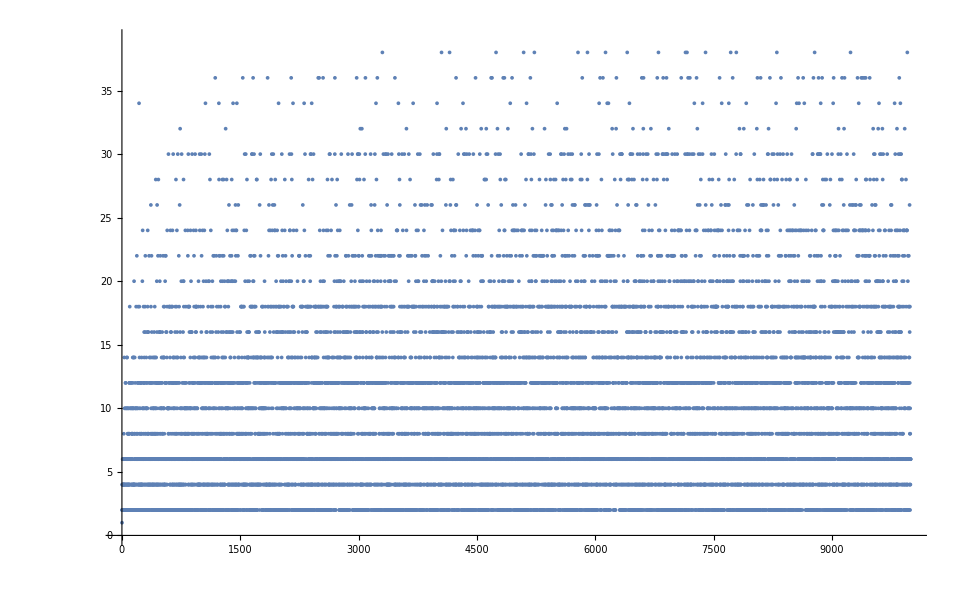

```mathematica
ListPlot[%62]
```

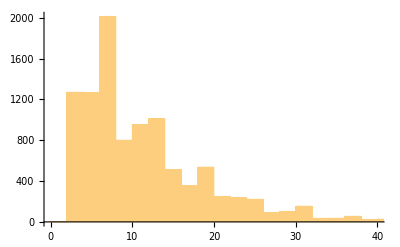

```mathematica
Histogram[%62]
```

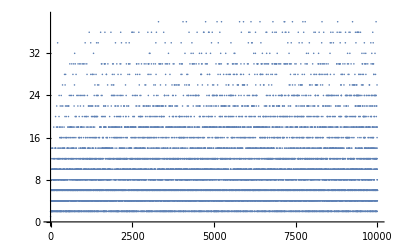

```mathematica
ListPlot[Out[62]]
```

```mathematica
Manipulate[
ListPlot[Out[62][[;;i]]]
,{i,1,Length@Out[62]}]
```

```mathematica
Manipulate[
ListPlot[Out[62][[;;i]]]
,{i,1,Length@Out[62],1}]
```

```mathematica
ComplexPlot3D[Gamma[z],{z,-5-5I,5+5I}]
```

-Graphics3D-

```mathematica
ComplexPlot3D[Gamma[z],{z,-5-5I,5+5I},AxesLabel->Automatic]
```

-Graphics3D-

```mathematica
ComplexPlot3D[z^2,{z,-5-5I,5+5I}]
```

-Graphics3D-

```mathematica
With[{a=10},
ComplexPlot3D[z^2,{z,-a-a ⅈ,a+a ⅈ}]
]
```

-Graphics3D-

```mathematica
√a ==c
```

√a==c

```mathematica
ApplySides[Function[x,x^2],√a ==c]
```

a==c^2

```mathematica
ApplySides[Function[x,a x],√a ==c]
```

a^(3/2)==a c

```mathematica
ApplySides[Function[x,x x],√a ==c]
```

a==c^2

```mathematica
ApplySides[Function[x,√a x],√a ==c]
```

a==√a c

```mathematica
√a c==c^2
```

√a c==c^2

```mathematica
Solve[√a c==c^2,a]
```

{{a→c^2}}

```mathematica
ListPlot[%62,Out[63]/2]
```

ListPlot::nonopt: Options expected (instead of /2) beyond position 1 in ListPlot[{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,«9949»},/2]. An option must be a rule or a list of rules.

ListPlot[{1,2,2,4,2,4,2,4,6,2,6,4,2,4,6,6,2,6,4,2,6,4,6,8,4,2,4,2,4,14,4,6,2,10,2,6,6,4,6,6,2,10,2,4,2,12,12,4,2,4,6,2,10,6,6,6,2,6,4,2,10,14,4,2,4,14,6,10,2,4,6,8,6,6,4,6,8,4,8,10,2,10,2,6,4,6,8,4,2,4,12,8,4,8,4,6,12,2,18,6,10,6,6,2,6,10,6,6,2,6,6,4,2,12,10,2,4,6,6,2,12,4,6,8,10,8,10,8,6,6,4,8,6,4,8,4,14,10,12,2,10,2,4,2,10,14,4,2,4,14,4,2,4,20,4,8,10,8,4,6,6,14,4,6,6,8,6,12,4,6,2,10,2,6,10,2,10,2,6,18,4,2,4,6,6,8,6,6,22,2,10,8,10,6,6,8,12,4,6,6,2,6,12,10,18,2,4,6,2,6,4,2,4,12,2,6,34,6,6,8,18,10,14,4,2,4,6,8,4,2,6,12,10,2,4,2,4,6,12,12,8,12,6,4,6,8,4,8,4,14,4,6,2,4,6,2,6,10,20,6,4,2,24,4,2,10,12,2,10,8,6,6,6,18,6,4,2,12,10,12,8,16,14,6,4,2,4,2,10,12,6,6,18,2,16,2,22,6,8,6,4,2,4,8,6,10,2,10,14,10,6,12,2,4,2,10,12,2,16,2,6,4,2,10,8,18,24,4,6,8,16,2,4,8,16,2,4,8,6,6,4,12,2,22,6,2,6,4,6,14,6,4,2,6,4,6,12,6,6,14,4,6,12,8,6,4,26,18,10,8,4,6,2,6,22,12,2,16,8,4,12,14,10,2,4,8,6,6,4,2,4,6,8,4,2,6,10,2,10,8,4,14,10,12,2,6,4,2,16,14,4,6,8,6,4,18,8,10,6,6,8,10,12,14,4,6,6,2,28,2,10,8,4,14,4,8,12,6,12,4,6,20,10,2,16,26,4,2,12,6,4,12,6,8,4,8,22,2,4,2,12,28,2,6,6,6,4,6,2,12,4,12,2,10,2,16,2,16,6,20,16,8,4,2,4,2,22,8,12,6,10,2,4,6,2,6,10,2,12,10,2,10,14,6,4,6,8,6,6,16,12,2,4,14,6,4,8,10,8,6,6,22,6,2,10,14,4,6,18,2,10,14,4,2,10,14,4,8,18,4,6,2,4,6,2,12,4,20,22,12,2,4,6,6,2,6,22,2,6,16,6,12,2,6,12,16,2,4,6,14,4,2,18,24,10,6,2,10,2,10,2,10,6,2,10,2,10,6,8,30,10,2,10,8,6,10,18,6,12,12,2,18,6,4,6,6,18,2,10,14,6,4,2,4,24,2,12,6,16,8,6,6,18,16,2,4,6,2,6,6,10,6,12,12,18,2,6,4,18,8,24,4,2,4,6,2,12,4,14,30,10,6,12,14,6,10,12,2,4,6,8,6,10,2,4,14,6,6,4,6,2,10,2,16,12,8,18,4,6,12,2,6,6,6,28,6,14,4,8,10,8,12,18,4,2,4,24,12,6,2,16,6,6,14,10,14,4,30,6,6,6,8,6,4,2,12,6,4,2,6,22,6,2,4,18,2,4,12,2,6,4,26,6,6,4,8,10,32,16,2,6,4,2,4,2,10,14,6,4,8,10,6,20,4,2,6,30,4,8,10,6,6,8,6,12,4,6,2,6,4,6,2,10,2,16,6,20,4,12,14,28,6,20,4,18,8,6,4,6,14,6,6,10,2,10,12,8,10,2,10,8,12,10,24,2,4,8,6,4,8,18,10,6,6,2,6,10,12,2,10,6,6,6,8,6,10,6,2,6,6,6,10,8,24,6,22,2,18,4,8,10,30,8,18,4,2,10,6,2,6,4,18,8,12,18,16,6,2,12,6,10,2,10,2,6,10,14,4,24,2,16,2,10,2,10,20,4,2,4,8,16,6,6,2,12,16,8,4,6,30,2,10,2,6,4,6,6,8,6,4,12,6,8,12,4,14,12,10,24,6,12,6,2,22,8,18,10,6,14,4,2,6,10,8,6,4,6,30,14,10,2,12,10,2,16,2,18,24,18,6,16,18,6,2,18,4,6,2,10,8,10,6,6,8,4,6,2,10,2,12,4,6,6,2,12,4,14,18,4,6,20,4,8,6,4,8,4,14,6,4,14,12,4,2,30,4,24,6,6,12,12,14,6,4,2,4,18,6,12,8,6,4,12,2,12,30,16,2,6,22,14,6,10,12,6,2,4,8,10,6,6,24,14,6,4,8,12,18,10,2,10,2,4,6,20,6,4,14,4,2,4,14,6,12,24,10,6,8,10,2,30,4,6,2,12,4,14,6,34,12,8,6,10,2,4,20,10,8,16,2,10,14,4,2,12,6,16,6,8,4,8,4,6,8,6,6,12,6,4,6,6,8,18,4,20,4,12,2,10,6,2,10,12,2,4,20,6,30,6,4,8,10,12,6,2,28,2,6,4,2,16,12,2,6,10,8,24,12,6,18,6,4,14,6,4,12,8,6,12,4,6,12,6,12,2,16,20,4,2,10,18,8,4,14,4,2,6,22,6,14,6,6,10,6,2,10,2,4,2,22,2,4,6,6,12,6,14,10,12,6,8,4,36,14,12,6,4,6,2,12,6,12,16,2,10,8,22,2,12,6,4,6,18,2,12,6,4,12,8,6,12,4,6,12,6,2,12,12,4,14,6,16,6,2,10,8,18,6,34,2,28,2,22,6,2,10,12,2,6,4,8,22,6,2,10,8,4,6,8,4,12,18,12,20,4,6,6,8,4,2,16,12,2,10,8,10,2,4,6,14,12,22,8,28,2,4,20,4,2,4,14,10,12,2,12,16,2,28,8,22,8,4,6,6,14,4,8,12,6,6,4,20,4,18,2,12,6,4,6,14,18,10,8,10,32,6,10,6,6,2,6,16,6,2,12,6,28,2,10,8,16,6,8,6,10,24,20,10,2,10,2,12,4,6,20,4,2,12,18,10,2,10,2,4,20,16,26,4,8,6,4,12,6,8,12,12,6,4,8,22,2,16,14,10,6,12,12,14,6,4,20,4,12,6,2,6,6,16,8,22,2,28,8,6,4,20,4,12,24,20,4,8,10,2,16,2,12,12,34,2,4,6,12,6,6,8,6,4,2,6,24,4,20,10,6,6,14,4,6,6,2,12,6,10,2,10,6,20,4,26,4,2,6,22,2,24,4,6,2,4,6,24,6,8,4,2,34,6,8,16,12,2,10,2,10,6,8,4,8,12,22,6,14,4,26,4,2,12,10,8,4,8,12,4,14,6,16,6,8,4,6,6,8,6,10,12,2,6,6,16,8,6,6,12,10,2,6,18,4,6,6,6,12,18,8,6,10,8,18,4,14,6,18,10,8,10,12,2,6,12,12,36,4,6,8,4,6,2,4,18,12,6,8,6,6,4,18,2,4,2,24,4,6,6,14,30,6,4,6,12,6,20,4,8,4,8,6,6,4,30,2,10,12,8,10,8,24,6,12,4,14,4,6,2,28,14,16,2,12,6,4,20,10,6,6,6,8,10,12,14,10,14,16,14,10,14,6,16,6,8,6,16,20,10,2,6,4,2,4,12,2,10,2,6,22,6,2,4,18,8,10,8,22,2,10,18,14,4,2,4,18,2,4,6,8,10,2,30,4,30,2,10,2,18,4,18,6,14,10,2,4,20,36,6,4,6,14,4,20,10,14,22,6,2,30,12,10,18,2,4,14,6,22,18,2,12,6,4,8,4,8,6,10,2,12,18,10,14,16,14,4,6,6,2,6,4,2,28,2,28,6,2,4,6,14,4,12,14,16,14,4,6,8,6,4,6,6,6,8,4,8,4,14,16,8,6,4,12,8,16,2,10,8,4,6,26,6,10,8,4,6,12,14,30,4,14,22,8,12,4,6,8,10,6,14,10,6,2,10,12,12,14,6,6,18,10,6,8,18,4,6,2,6,10,2,10,8,6,6,10,2,18,10,2,12,4,6,8,10,12,14,12,4,8,10,6,6,20,4,14,16,14,10,8,10,12,2,18,6,12,10,12,2,4,2,12,6,4,8,4,44,4,2,4,2,10,12,6,6,14,4,6,6,6,8,6,36,18,4,6,2,12,6,6,6,4,14,22,12,2,18,10,6,26,24,4,2,4,2,4,14,4,6,6,8,16,12,2,42,4,2,4,24,6,6,2,18,4,14,6,28,18,14,6,10,12,2,6,12,30,6,4,6,6,14,4,2,24,4,6,6,26,10,18,6,8,6,6,30,4,12,12,2,16,2,6,4,12,18,2,6,4,26,12,6,12,4,24,24,12,6,2,12,28,8,4,6,12,2,18,6,4,6,6,20,16,2,6,6,18,10,6,2,4,8,6,6,24,16,6,8,10,6,14,22,8,16,6,2,12,4,2,22,8,18,34,2,6,18,4,6,6,8,10,8,18,6,4,2,4,8,16,2,12,12,6,18,4,6,6,6,2,6,12,10,20,12,18,4,6,2,16,2,10,14,4,30,2,10,12,2,24,6,16,8,10,2,12,22,6,2,16,20,10,2,12,12,18,10,12,6,2,10,2,6,10,18,2,12,6,4,6,2,24,28,2,4,2,10,2,16,12,8,22,2,6,4,2,10,6,20,12,10,8,12,6,6,6,4,18,2,4,12,18,2,12,6,4,2,16,12,12,14,4,8,18,4,12,14,6,6,4,8,6,4,20,12,10,14,4,2,16,2,12,30,4,6,24,20,24,10,8,12,10,12,6,12,12,6,8,16,14,6,4,6,36,20,10,30,12,2,4,2,28,12,14,6,22,8,4,18,6,14,18,4,6,2,6,34,18,2,16,6,18,2,24,4,2,6,12,6,12,10,8,6,16,12,8,10,14,40,6,2,6,4,12,14,4,2,4,2,4,8,6,10,6,6,2,6,6,6,12,6,24,10,2,10,6,12,6,6,14,6,6,52,20,6,10,2,10,8,10,12,12,2,6,4,14,16,8,12,6,22,2,10,8,6,22,2,22,6,8,10,12,12,2,10,6,12,2,4,14,10,2,6,18,4,12,8,18,12,6,6,4,6,6,14,4,2,12,12,4,6,18,18,12,2,16,12,8,18,10,26,4,6,8,6,6,4,2,10,20,4,6,8,4,20,10,2,34,2,4,24,2,12,12,10,6,2,12,30,6,12,16,12,2,22,18,12,14,10,2,12,12,4,2,4,6,12,2,16,18,2,40,8,16,6,8,10,2,4,18,8,10,8,12,4,18,2,18,10,2,4,2,4,8,28,2,6,22,12,6,14,18,4,6,8,6,6,10,8,4,2,18,10,6,20,22,8,6,30,4,2,4,18,6,30,2,4,8,6,4,6,12,14,34,14,6,4,2,6,4,14,4,2,6,28,2,4,6,8,10,2,10,2,10,2,4,30,2,12,12,10,18,12,14,10,2,12,6,10,6,14,12,4,14,4,18,2,10,8,4,8,10,12,18,18,8,6,18,16,14,6,6,10,14,4,6,2,12,12,4,6,6,12,2,16,2,12,6,4,14,6,4,2,12,18,4,36,18,12,12,2,4,2,4,8,12,4,36,6,18,2,12,10,6,12,24,8,6,6,16,12,2,18,10,20,10,2,6,18,4,2,40,6,2,16,2,4,8,18,10,12,6,2,10,8,4,6,12,2,10,18,8,6,4,20,4,6,36,6,2,10,6,24,6,14,16,6,18,2,10,20,10,8,6,4,6,2,10,2,12,4,2,4,8,10,6,12,18,14,12,16,8,6,16,8,4,2,6,18,24,18,10,12,2,4,14,10,6,6,6,18,12,2,28,18,14,16,12,14,24,12,22,6,2,10,8,4,2,4,14,12,6,4,6,14,4,2,4,30,6,2,6,10,2,30,22,2,4,6,8,6,6,16,12,12,6,8,4,2,24,12,4,6,8,6,6,10,2,6,12,28,14,6,4,12,8,6,12,4,6,14,6,12,10,6,6,8,6,6,4,2,4,8,12,4,14,18,10,2,16,6,20,6,10,8,4,30,36,12,8,22,12,2,6,12,16,6,6,2,18,4,26,4,8,18,10,8,10,6,14,4,20,22,18,12,8,28,12,6,6,8,6,12,24,16,14,4,14,12,6,10,12,20,6,4,8,18,12,18,10,2,4,20,10,14,4,6,2,10,24,18,2,4,20,16,14,10,14,6,4,6,20,6,10,6,2,12,6,30,10,8,6,4,6,8,40,2,4,2,12,18,4,6,8,10,6,18,18,2,12,16,8,6,4,6,6,2,52,14,4,20,16,2,4,6,12,2,6,12,12,6,4,14,10,6,6,14,10,14,16,8,6,12,4,8,22,6,2,18,22,6,2,18,6,16,14,10,6,12,2,6,4,8,18,12,16,2,4,14,4,8,12,12,30,16,8,4,2,6,22,12,8,10,6,6,6,14,6,18,10,12,2,10,2,4,26,4,12,8,4,18,8,10,14,16,6,6,8,10,6,8,6,12,10,20,10,8,4,12,26,18,4,12,18,6,30,6,8,6,22,12,2,4,6,6,2,10,2,4,6,6,2,6,22,18,6,18,12,8,12,6,10,12,2,16,2,10,2,10,18,6,20,4,2,6,22,6,6,18,6,14,12,16,2,6,6,4,14,12,4,2,18,16,36,12,6,14,28,2,12,6,12,6,4,2,16,30,8,24,6,30,10,2,18,4,6,12,8,22,2,6,22,18,2,10,2,10,30,2,28,6,14,16,6,20,16,2,6,4,32,4,2,4,6,2,12,4,6,6,12,2,6,4,6,8,6,4,20,4,32,10,8,16,2,22,2,4,6,8,6,16,14,4,18,8,4,20,6,12,12,6,10,2,10,2,12,28,12,18,2,18,10,8,10,48,2,4,6,8,10,2,10,30,2,36,6,10,6,2,18,4,6,8,16,14,16,6,14,4,20,4,6,2,10,12,2,6,12,6,6,4,12,2,6,4,12,6,8,4,2,6,18,10,6,8,12,6,22,2,6,12,18,4,14,6,4,20,6,16,8,4,8,22,8,12,6,6,16,12,18,30,8,4,2,4,6,26,4,14,24,22,6,2,6,10,6,14,6,6,12,10,6,2,12,10,12,8,18,18,10,6,8,16,6,6,8,16,20,4,2,10,2,10,12,6,8,6,10,20,10,18,26,4,6,30,2,4,8,6,12,12,18,4,8,22,6,2,12,34,6,18,12,6,2,28,14,16,14,4,14,12,4,6,6,2,36,4,6,20,12,24,6,22,2,16,18,12,12,18,2,6,6,6,4,6,14,4,2,22,8,12,6,10,6,8,12,18,12,6,10,2,22,14,6,6,4,18,6,20,22,2,12,24,4,18,18,2,22,2,4,12,8,12,10,14,4,2,18,16,38,6,6,6,12,10,6,12,8,6,4,6,14,30,6,10,8,22,6,8,12,10,2,10,2,6,10,2,10,12,18,20,6,4,8,22,6,6,30,6,14,6,12,12,6,10,2,10,30,2,16,8,4,2,6,18,4,2,6,4,26,4,8,6,10,2,4,6,8,4,6,30,12,2,6,6,4,20,22,8,4,2,4,72,8,4,8,22,2,4,14,10,2,4,20,6,10,18,6,20,16,6,8,6,4,20,12,22,2,4,2,12,10,18,2,22,6,18,30,2,10,14,10,8,16,50,6,10,8,10,12,6,18,2,22,6,2,4,6,8,6,6,10,18,2,22,2,16,14,10,6,2,12,10,20,4,14,6,4,36,2,4,6,12,2,4,14,12,6,4,6,2,6,4,20,10,2,10,6,12,2,24,12,12,6,6,4,24,2,4,24,2,6,4,6,8,16,6,2,10,12,14,6,34,6,14,6,4,2,30,22,8,4,6,8,4,2,28,2,6,4,26,18,22,2,6,16,6,2,16,12,2,12,4,6,6,14,10,6,8,12,4,18,2,10,8,16,6,6,30,2,10,18,2,10,8,4,8,12,24,40,2,12,10,6,12,2,12,4,2,4,6,18,14,12,6,4,14,30,4,8,10,8,6,10,18,8,4,14,16,6,8,4,6,2,10,2,12,4,2,4,6,8,4,6,32,24,10,8,18,10,2,6,10,2,4,18,6,12,2,16,2,22,6,6,8,18,4,18,12,8,6,4,20,6,30,22,12,2,6,18,4,62,4,2,12,6,10,2,12,12,28,2,4,14,22,6,2,6,6,10,14,4,2,10,6,8,10,14,10,6,2,12,22,18,8,10,18,12,2,12,4,12,2,10,2,6,18,6,6,34,6,2,12,4,6,18,18,2,16,6,6,8,6,10,18,8,10,8,10,2,4,18,26,12,22,2,4,2,22,6,6,14,16,6,20,10,12,2,18,42,4,24,2,6,10,12,2,6,10,8,4,6,12,12,8,4,6,12,30,20,6,24,6,10,12,2,10,20,6,6,4,12,14,10,18,12,8,6,12,4,14,10,2,12,30,16,2,12,6,4,2,4,6,26,4,18,2,4,6,14,54,6,52,2,16,6,6,12,26,4,2,6,22,6,2,12,12,6,10,18,2,12,12,10,18,12,6,8,6,10,6,8,4,2,4,20,24,6,6,10,14,10,2,22,6,14,10,26,4,18,8,12,12,10,12,6,8,16,6,8,6,6,22,2,10,20,10,6,44,18,6,10,2,4,6,14,4,26,4,2,12,10,8,4,8,12,4,12,8,22,8,6,10,18,6,6,8,6,12,4,8,18,10,12,6,12,2,6,4,2,16,12,12,14,10,14,6,10,12,2,12,6,4,6,2,12,4,26,6,18,6,10,6,2,18,10,8,4,26,10,20,6,16,20,12,10,8,10,2,16,6,20,10,20,4,30,2,4,8,16,2,18,4,2,6,10,18,12,14,18,6,16,20,6,4,8,6,4,6,12,8,10,2,12,6,4,2,6,10,2,16,12,14,10,6,8,6,28,2,6,18,30,34,2,16,12,2,18,16,6,8,10,8,10,8,10,44,6,6,4,20,4,2,4,14,28,8,6,16,14,30,6,30,4,14,10,6,6,8,4,18,12,6,2,22,12,8,6,12,4,14,4,6,2,4,18,20,6,16,38,16,2,4,6,2,40,42,14,4,6,2,24,10,6,2,18,10,12,2,16,2,6,16,6,8,4,2,10,6,8,10,2,18,16,8,12,18,12,6,12,10,6,6,18,12,14,4,2,10,20,6,12,6,16,26,4,18,2,4,32,10,8,6,4,6,6,14,6,18,4,2,18,10,8,10,8,10,2,4,6,2,10,42,8,12,4,6,18,2,16,8,4,2,10,14,12,10,20,4,8,10,38,4,6,2,10,20,10,12,6,12,26,12,4,8,28,8,4,8,24,6,10,8,6,16,12,8,10,12,8,22,6,2,10,2,6,10,6,6,8,6,4,14,28,8,16,18,8,4,6,20,4,18,6,2,24,24,6,6,12,12,4,2,22,2,10,6,8,12,4,20,18,6,4,12,24,6,6,54,8,6,4,26,36,4,2,4,26,12,12,4,6,6,8,12,10,2,12,16,18,6,8,6,12,18,10,2,54,4,2,10,30,12,8,4,8,16,14,12,6,4,6,12,6,2,4,14,12,4,14,6,24,6,6,10,12,12,20,18,6,6,16,8,4,6,20,4,32,4,14,10,2,6,12,16,2,4,6,12,2,10,8,6,4,2,10,14,6,6,12,18,34,8,10,6,24,6,2,10,12,2,30,10,14,12,12,16,6,6,2,18,4,6,30,14,4,6,6,2,6,4,6,14,6,4,8,10,12,6,32,10,8,22,2,10,6,24,8,4,30,6,2,12,16,8,6,4,6,8,16,14,6,6,4,2,10,12,2,16,14,4,2,4,20,18,10,2,10,6,12,30,8,18,12,10,2,6,6,4,12,12,2,4,12,18,24,2,10,6,8,16,8,6,12,10,14,6,12,6,6,4,2,24,4,6,8,6,4,2,4,6,14,4,8,10,24,24,12,2,6,12,22,30,2,6,18,10,6,6,8,4,2,6,10,8,10,6,8,16,6,14,6,4,24,8,10,2,12,6,4,36,2,22,6,8,6,10,8,6,12,10,14,10,6,18,12,2,12,4,26,10,14,16,18,8,18,12,12,6,16,14,24,10,12,8,22,6,2,10,60,6,2,4,8,16,14,10,6,24,6,12,18,24,2,30,4,2,12,6,10,2,4,14,6,16,2,10,8,22,20,6,4,32,6,18,4,2,4,2,4,8,52,14,22,2,22,20,10,8,10,2,6,4,14,4,6,20,4,6,2,12,12,6,12,16,2,12,10,8,4,6,2,28,12,8,10,12,2,4,14,28,8,6,4,2,4,6,2,12,58,6,14,10,2,6,28,32,4,30,8,6,4,6,12,12,2,4,6,6,14,16,8,30,4,2,10,8,6,4,6,26,4,12,2,10,18,12,12,18,2,4,12,8,12,10,20,4,8,16,12,8,6,16,8,10,12,14,6,4,8,12,4,20,6,40,8,16,6,36,2,6,4,6,2,22,18,2,10,6,36,14,12,4,18,8,4,14,10,2,10,8,4,2,18,16,12,14,10,14,6,6,42,10,6,6,20,10,8,12,4,12,18,2,10,14,18,10,18,8,6,4,14,6,10,30,14,6,6,4,12,38,4,2,4,6,8,12,10,6,18,6,50,6,4,6,12,8,10,32,6,22,2,10,12,18,2,6,4,30,8,6,6,18,10,2,4,12,20,10,8,24,10,2,6,22,6,2,18,10,12,2,30,18,12,28,2,6,4,6,14,6,12,10,8,4,12,26,10,8,6,16,2,10,18,14,6,4,6,14,16,2,6,4,12,20,4,20,4,6,12,2,36,4,6,2,10,2,22,8,6,10,12,12,18,14,24,36,4,20,24,10,6,2,28,6,18,8,4,6,8,6,4,2,12,28,18,14,16,14,18,10,8,6,4,6,6,8,22,12,2,10,18,6,2,18,10,2,12,10,18,32,6,4,6,6,8,6,6,10,20,6,12,10,8,10,14,6,10,14,4,2,22,18,2,10,2,4,20,4,2,34,2,12,6,10,2,10,18,6,14,12,12,22,8,6,16,6,8,4,12,6,8,4,36,6,6,20,24,6,12,18,10,2,10,26,6,16,8,6,4,24,18,8,12,12,10,18,12,2,24,4,12,18,12,14,10,2,4,24,12,14,10,6,2,6,4,6,26,4,6,6,2,22,8,18,4,18,8,4,24,2,12,12,4,2,52,2,18,6,4,6,12,2,6,12,10,8,4,2,24,10,2,10,2,12,6,18,40,6,20,16,2,12,6,10,12,2,4,6,14,12,12,22,6,8,4,2,16,18,12,2,6,16,6,2,6,4,12,30,8,16,2,18,10,24,2,6,24,4,2,22,2,16,2,6,12,4,18,8,4,14,4,18,24,6,2,6,10,2,10,38,6,10,14,6,6,24,4,2,12,16,14,16,12,2,6,10,26,4,2,12,6,4,12,8,12,10,18,6,14,28,2,6,10,2,4,14,34,2,6,22,2,10,14,4,2,16,8,10,6,8,10,8,4,6,2,16,6,6,18,30,14,6,4,30,2,10,14,4,20,10,8,4,8,18,4,14,6,4,24,6,6,18,18,2,36,6,10,14,12,4,6,2,30,6,4,2,6,28,20,4,20,12,24,16,18,12,14,6,4,12,32,12,6,10,8,10,6,18,2,16,14,6,22,6,12,2,18,4,8,30,12,4,12,2,10,38,22,2,4,14,6,12,24,4,2,4,14,12,10,2,16,6,20,4,20,22,12,2,4,2,12,22,24,6,6,2,6,4,6,2,10,12,12,6,2,6,16,8,6,4,18,12,12,14,4,12,6,8,6,18,6,10,12,14,6,4,8,22,6,2,28,18,2,18,10,6,14,10,2,10,14,6,10,2,22,6,8,6,16,12,8,22,2,4,14,18,12,6,24,6,10,2,12,22,18,6,20,6,10,14,4,2,6,12,22,14,12,4,6,8,22,2,10,12,8,40,2,6,10,8,4,42,20,4,32,12,10,6,12,12,2,10,8,6,4,8,4,26,18,4,8,28,6,18,6,12,2,10,6,6,14,10,12,14,24,6,4,20,22,2,18,4,6,12,2,16,18,14,6,6,4,6,8,18,4,14,30,4,18,8,10,2,4,8,12,4,12,18,2,12,10,2,16,8,4,30,2,6,28,2,10,2,18,10,14,4,26,6,18,4,20,6,4,8,18,4,12,26,24,4,20,22,2,18,22,2,4,12,2,6,6,6,4,6,14,4,24,12,6,18,2,12,28,14,4,6,8,22,6,12,18,8,4,20,6,4,6,2,18,6,4,12,12,8,28,6,8,10,2,24,12,10,24,8,10,20,12,6,12,12,4,14,12,24,34,18,8,10,6,18,8,4,8,16,14,6,4,6,24,2,6,4,6,2,16,6,6,20,24,4,2,4,14,4,18,2,6,12,4,14,4,2,18,16,6,6,2,16,20,6,6,30,4,8,6,24,16,6,6,8,12,30,4,18,18,8,4,26,10,2,22,8,10,14,6,4,18,8,12,28,2,6,4,12,6,24,6,8,10,20,16,8,30,6,6,4,2,10,14,6,10,32,22,18,2,4,2,4,8,22,8,18,12,28,2,16,12,18,14,10,18,12,6,32,10,14,6,10,2,10,2,6,22,2,4,6,8,10,6,14,6,4,12,30,24,6,6,8,6,4,2,4,6,8,6,6,22,18,8,4,2,18,6,4,2,16,18,20,10,6,6,30,2,12,28,6,6,6,2,12,10,8,18,18,4,8,18,10,2,28,2,10,14,4,2,30,12,22,26,10,8,6,10,8,16,14,6,6,10,14,6,4,2,10,12,2,6,10,8,4,2,10,26,22,6,2,12,18,4,26,4,8,10,6,14,10,2,18,6,10,20,6,6,4,24,2,4,8,6,16,14,16,18,2,4,12,2,10,2,6,12,10,6,6,20,6,4,6,38,4,6,12,14,4,12,8,10,12,12,8,4,6,14,10,6,12,2,10,18,2,18,10,8,10,2,12,4,14,28,2,16,2,18,6,10,6,8,16,14,30,10,20,6,10,24,2,28,2,12,16,6,8,36,4,8,4,14,12,10,8,12,4,6,8,4,6,14,22,8,6,4,2,10,6,20,10,8,6,6,22,18,2,16,6,20,4,26,4,14,22,14,4,12,6,8,4,6,6,26,10,2,18,18,4,2,16,2,18,4,6,8,4,6,12,2,6,6,28,38,4,8,16,26,4,2,10,12,2,10,8,6,10,12,2,10,2,24,4,30,26,6,6,18,6,6,22,2,10,18,26,4,18,8,6,6,12,16,6,8,16,6,8,16,2,42,58,8,4,6,2,4,8,16,6,20,4,12,12,6,12,2,10,2,6,22,2,10,6,8,6,10,14,6,6,4,18,8,10,8,16,14,10,2,10,2,12,6,4,20,10,8,52,8,10,6,2,10,8,10,6,6,8,10,2,22,2,4,6,14,4,2,24,12,4,26,18,4,6,14,30,6,4,6,2,22,8,4,6,2,22,6,8,16,6,14,4,6,18,8,12,6,12,24,30,16,8,34,8,22,6,14,10,18,14,4,12,8,4,36,6,6,2,10,2,4,20,6,6,10,12,6,2,40,8,6,28,6,2,12,18,4,24,14,6,6,10,20,10,14,16,14,16,6,8,36,4,12,12,6,12,50,12,6,4,6,6,8,6,10,2,10,2,18,10,14,16,8,6,4,20,4,2,10,6,14,18,10,38,10,18,2,10,2,12,4,2,4,14,6,10,8,40,6,20,4,12,8,6,34,8,22,8,12,10,2,16,42,12,8,22,8,22,8,6,34,2,6,4,14,6,16,2,22,6,8,24,22,6,2,12,4,6,14,4,8,24,4,6,6,2,22,20,6,4,14,4,6,6,8,6,10,6,8,6,16,14,6,6,22,6,24,32,6,18,6,18,10,8,30,18,6,16,12,6,12,2,6,4,12,8,6,22,8,6,4,14,10,18,20,10,2,6,4,2,28,18,2,10,6,6,6,14,40,24,2,4,8,12,4,20,4,32,18,16,6,36,8,6,4,6,14,4,6,26,6,10,14,18,10,6,6,14,10,6,6,14,6,24,4,14,22,8,12,10,8,12,18,10,18,8,24,10,8,4,24,6,18,6,2,10,30,2,10,2,4,2,40,2,28,8,6,6,18,6,10,14,4,18,30,18,2,12,30,6,30,4,18,12,2,4,14,6,10,6,8,6,10,12,2,6,12,10,2,18,4,20,4,6,14,6,6,22,6,6,8,18,18,10,2,10,2,6,4,6,12,18,2,10,8,4,18,2,6,6,6,10,8,10,6,18,12,8,12,6,4,6,14,16,2,12,4,6,38,6,6,16,20,28,20,10,6,6,14,4,26,4,14,10,18,14,28,2,4,14,16,2,28,6,8,6,34,8,4,18,2,16,8,6,40,8,18,4,30,6,12,2,30,6,10,14,40,14,10,2,12,10,8,4,8,6,6,28,2,4,12,14,16,8,30,16,18,2,10,18,6,32,4,18,6,2,12,10,18,2,6,10,14,18,28,6,8,16,2,4,20,10,8,18,10,2,10,8,4,6,12,6,20,4,2,6,4,20,10,26,18,10,2,18,6,16,14,4,26,4,14,10,12,14,6,6,4,14,10,2,30,18,22,2,16,2,4,8,6,6,16,2,6,12,10,8,12,4,14,4,6,20,10,12,2,6,6,4,2,10,2,30,16,12,20,18,4,6,2,4,8,16,14,18,22,6,2,22,6,6,18,2,10,36,8,4,6,20,4,12,6,14,4,2,28,24,8,4,6,12,30,18,32,22,8,36,6,4,12,2,12,4,6,20,10,18,18,8,6,4,24,8,10,14,6,4,8,12,16,2,16,6,8,16,12,14,10,30,14,4,12,8,12,6,10,2,12,28,6,12,12,20,10,2,10,14,6,6,30,4,8,12,4,2,10,14,4,26,18,12,10,6,8,4,12,6,24,18,8,10,2,12,4,12,12,6,2,22,2,4,2,12,16,14,10,2,16,18,32,4,6,20,22,8,10,2,10,6,2,4,14,6,24,4,8,4,6,12,12,8,6,10,12,8,10,2,10,12,6,12,12,20,28,20,10,14,10,8,10,6,2,4,14,6,6,12,6,12,10,14,10,14,16,8,10,26,4,2,6,4,14,4,6,12,8,6,30,18,12,6,12,16,12,12,2,28,6,14,10,36,2,4,6,8,12,22,18,2,30,18,22,20,18,10,38,6,4,2,24,4,6,6,2,10,6,14,10,8,4,24,14,16,14,22,6,20,10,14,4,12,12,2,16,8,6,6,18,4,6,14,22,6,2,42,16,2,10,6,2,4,6,8,10,20,16,30,8,10,8,10,2,30,6,6,36,10,8,16,6,2,12,28,2,4,6,18,12,6,8,10,2,4,50,4,20,4,30,8,4,6,12,2,24,4,8,18,6,4,6,8,10,2,4,2,40,18,36,30,30,8,16,14,6,12,28,2,22,2,4,12,30,12,6,2,4,14,10,2,18,22,12,18,2,10,18,32,6,4,2,6,10,20,12,10,6,12,20,12,6,4,2,16,2,16,6,14,4,2,16,2,6,16,6,8,4,8,22,18,8,12,4,8,6,24,22,6,2,12,30,6,10,12,6,2,22,6,2,12,6,22,8,12,22,2,10,6,18,12,2,6,12,18,6,4,20,22,8,12,24,16,14,10,30,18,2,6,4,14,10,2,12,10,12,6,2,16,12,2,6,12,10,2,10,6,2,12,12,16,20,10,12,8,30,10,14,4,6,8,6,4,20,18,24,4,12,8,4,2,24,6,24,10,2,4,6,2,6,6,6,4,24,2,10,12,2,6,10,8,6,10,18,2,6,4,20,24,10,12,2,12,6,24,4,36,14,16,8,22,6,8,4,2,6,22,20,16,12,18,2,12,16,6,6,12,6,12,2,6,12,10,8,16,8,6,16,8,12,4,6,6,20,12,12,4,6,20,4,12,2,10,2,6,30,22,6,2,4,38,10,2,4,2,22,2,16,2,6,10,20,6,24,4,12,14,12,4,38,10,30,6,2,12,12,4,6,30,14,4,8,18,36,4,6,20,4,2,12,10,2,6,10,12,6,12,8,6,6,24,4,30,20,6,36,10,2,12,6,4,8,6,4,12,8,6,12,4,6,14,4,20,12,4,6,18,2,4,18,2,16,12,30,6,6,8,40,8,48,6,16,18,14,12,6,18,4,20,10,2,6,10,8,30,4,12,20,6,12,6,6,34,6,6,18,6,8,10,12,6,8,10,2,4,24,6,8,22,6,2,12,6,10,12,6,24,6,14,12,36,4,24,2,10,8,10,6,14,10,32,4,8,10,12,26,18,4,6,20,4,20,6,16,6,2,30,12,6,10,2,6,10,12,8,4,2,6,10,12,26,22,8,6,4,14,6,6,30,4,6,14,4,2,28,2,6,22,8,4,18,18,18,2,12,6,4,20,10,6,6,14,10,12,2,12,30,34,12,8,6,4,2,10,2,16,12,2,10,8,18,24,6,4,12,14,4,8,4,14,4,6,6,20,6,4,8,18,52,2,4,12,8,4,38,4,26,24,16,12,6,2,12,12,16,2,6,6,4,12,14,16,8,12,18,16,6,8,10,6,14,10,12,2,10,2,4,24,6,42,24,8,10,6,6,6,2,12,4,14,6,6,28,6,2,10,12,12,6,20,4,6,14,4,2,12,10,12,24,6,8,6,6,4,24,12,20,16,14,30,18,6,4,26,12,4,6,2,6,4,2,28,8,40,2,10,8,4,20,6,18,10,2,4,44,6,18,12,6,4,6,2,22,6,14,30,10,24,2,10,8,16,18,2,18,22,8,10,6,6,14,4,8,18,4,2,18,18,18,6,4,24,18,2,16,6,6,18,20,16,20,4,14,6,4,20,18,10,2,6,10,24,2,10,24,6,6,24,6,12,2,28,12,14,6,6,12,6,22,12,12,8,36,4,12,14,4,20,10,12,24,2,4,6,12,2,4,2,10,12,26,6,16,8,4,8,10,8,6,34,2,12,16,24,6,2,10,2,18,4,8,6,16,6,2,6,6,6,4,14,4,20,6,4,20,6,12,22,6,2,10,12,2,6,4,8,12,4,14,12,10,14,4,12,26,10,14,4,26,6,30,4,18,18,8,6,16,8,10,14,10,8,10,20,22,20,16,2,18,6,4,6,6,12,2,10,26,4,8,18,18,6,18,6,4,6,24,6,20,34,26,10,2,28,12,8,10,12,2,6,22,2,12,16,2,6,6,10,14,16,20,6,4,38,6,10,6,8,16,42,2,6,4,6,6,6,14,16,14,4,20,10,2,4,8,18,10,12,36,2,10,42,8,4,20,24,16,8,22,6,8,4,2,6,22,6,6,8,28,2,10,18,14,6,4,18,8,10,14,4,12,8,10,12,14,4,2,12,12,4,6,18,30,12,38,6,12,10,2,18,10,12,8,4,8,6,4,2,24,12,18,4,2,4,2,58,12,8,24,10,2,4,6,6,12,2,4,14,6,6,16,12,2,4,32,4,24,6,6,8,10,2,22,18,12,20,6,30,4,30,6,2,4,14,6,4,14,16,2,12,10,2,6,12,12,10,6,8,22,8,12,12,6,16,6,18,20,22,18,2,22,2,16,2,22,14,10,20,10,32,4,8,10,6,2,22,6,12,2,6,4,2,4,14,12,24,10,2,12,16,2,4,6,14,6,10,12,2,16,14,34,12,2,6,6,6,4,20,10,26,12,12,4,2,4,8,10,2,4,2,22,6,6,14,4,18,12,26,6,10,8,16,2,4,20,10,6,42,2,10,6,8,24,12,6,4,6,12,2,28,8,12,18,18,6,46,8,10,6,14,4,2,6,4,6,42,8,10,8,10,2,18,4,6,12,12,2,4,20,10,12,12,8,4,26,18,22,8,6,16,14,16,2,18,10,2,6,6,10,14,4,2,30,4,2,4,8,10,6,2,12,16,6,56,10,2,12,10,8,12,6,4,14,10,2,4,8,6,4,20,6,12,22,6,32,10,2,10,12,14,6,28,36,6,6,2,12,4,6,6,8,22,2,18,10,2,6,4,20,10,8,4,6,14,18,6,42,22,2,4,2,28,2,4,18,6,6,6,12,2,24,10,36,6,2,12,10,26,24,18,16,6,6,14,24,12,4,8,6,12,4,8,16,20,40,26,4,12,2,6,4,2,10,14,10,2,4,26,12,28,2,16,26,6,10,2,6,10,6,8,6,6,6,10,12,6,20,40,20,4,2,16,12,6,12,8,4,18,2,12,10,26,12,16,2,18,24,12,4,14,22,20,10,14,12,4,18,12,8,10,12,6,30,14,4,24,6,30,6,6,2,6,22,32,6,4,6,6,20,16,2,10,8,12,10,2,6,10,8,16,36,8,6,4,2,28,2,28,12,2,10,6,14,10,6,6,6,8,6,4,14,18,4,6,12,2,10,18,8,30,40,2,18,4,6,14,18,6,4,12,6,12,6,14,10,26,6,16,2,16,30,2,10,2,42,6,28,14,6,10,2,12,18,12,6,10,12,12,20,6,4,2,10,6,12,12,14,12,34,6,2,12,10,6,8,6,4,12,38,6,10,18,2,28,2,6,12,30,16,2,10,8,4,2,16,18,26,4,6,8,18,22,6,20,4,6,12,2,6,12,4,18,6,2,22,12,8,6,16,18,30,12,24,2,10,2,6,6,4,6,36,14,6,22,2,58,8,12,6,10,2,40,8,6,28,2,4,14,6,6,18,10,8,4,14,4,8,30,4,6,8,6,6,18,4,2,4,14,12,18,10,2,4,12,2,10,8,10,14,10,18,12,8,6,10,14,10,8,22,2,6,22,12,6,8,12,28,2,48,12,4,18,8,10,14,10,14,4,12,30,24,6,8,6,4,8,54,4,2,10,12,8,10,12,12,18,2,24,4,8,22,12,20,4,12,2,12,16,2,28,2,6,24,10,2,28,2,4,20,4,12,6,14,4,6,14,22,24,20,4,14,6,6,10,30,8,10,18,2,6,6,16,2,6,6,4,2,24,4,2,24,10,6,2,10,2,6,22,8,4,8,6,4,18,2,18,4,8,16,26,4,6,8,22,20,16,8,4,6,24,6,14,12,16,2,12,4,14,10,2,4,12,18,32,10,14,24,12,40,8,34,12,14,4,18,2,28,12,20,6,10,2,40,18,14,12,4,36,6,2,22,6,14,10,24,42,2,16,2,34,8,6,4,2,4,14,40,8,12,6,24,18,4,6,2,6,4,2,4,2,24,10,8,6,6,10,14,6,16,18,14,18,24,4,6,6,8,4,20,10,6,12,2,12,4,14,6,6,6,4,14,16,36,14,6,4,14,4,6,24,8,4,20,10,14,12,34,8,10,6,6,6,14,4,14,12,6,10,18,14,10,12,6,2,6,6,28,2,4,24,6,2,4,8,16,6,20,4,2,10,2,10,8,64,6,8,12,4,14,12,10,2,12,6,10,18,24,6,2,10,8,6,16,20,4,14,6,6,12,6,4,6,2,4,8,22,6,8,4,2,16,18,14,6,22,14,10,14,4,6,2,4,14,10,12,8,16,8,10,8,24,40,6,12,2,6,18,4,2,4,30,2,30,4,8,18,12,12,4,2,4,14,36,16,18,2,12,10,6,12,18,2,18,6,6,22,18,38,6,10,18,2,10,8,6,16,24,14,6,4,6,14,16,24,6,12,8,12,10,14,46,2,16,2,22,6,2,10,2,10,2,6,4,20,10,6,30,8,6,6,4,30,8,6,6,6,22,36,2,4,8,6,6,4,14,12,10,20,4,2,4,30,6,14,16,12,30,2,4,6,8,30,10,8,34,18,12,8,22,20,4,14,10,20,6,4,2,10,14,4,26,6,36,12,18,4,8,6,4,6,2,28,6,6,24,8,10,26,6,24,4,8,24,10,20,4,2,10,14,16,2,6,6,4,6,8,18,28,14,6,16,14,6,4,6,6,8,4,2,4,12,2,12,6,12,28,2,6,12,10,14,4,44,6,10,2,12,12,30,4,12,2,6,10,12,2,10,2,10,6,8,10,6,14,16,8,6,12,10,2,10,8,12,10,18,8,4,2,4,26,6,22,6,14,10,6,2,28,6,8,46,6,6,18,6,6,8,6,10,18,2,6,12,18,10,8,12,30,10,2,10,2,4,6,18,2,4,20,12,4,6,8,34,6,6,24,12,8,36,16,2,6,4,2,4,6,20,6,24,4,2,4,18,20,6,22,8,46,18,2,16,20,22,2,24,22,2,16,24,20,16,2,4,8,10,2,10,14,4,8,18,4,8,4,14,10,2,24,16,8,6,16,20,10,2,6,4,30,2,16,32,6,12,10,24,8,12,18,16,2,12,6,4,12,6,2,28,18,2,22,6,6,6,2,6,16,14,6,30,16,2,10,2,4,12,2,12,10,14,6,10,8,28,2,36,6,16,14,4,20,24,6,4,8,4,18,8,4,14,4,6,2,24,16,14,4,26,16,2,10,32,6,4,6,12,6,36,8,12,4,2,4,8,6,4,20,12,10,24,12,2,12,10,6,12,2,6,18,4,6,6,6,8,24,6,10,12,30,14,10,8,12,6,10,12,2,18,6,4,8,4,24,20,4,8,10,12,8,12,16,6,14,4,8,4,18,50,6,6,4,6,8,6,10,26,10,6,2,10,2,10,6,38,12,4,8,10,20,6,6,6,18,10,2,12,16,2,12,12,4,26,10,6,20,18,40,12,8,10,12,2,18,12,10,2,10,26,4,6,12,8,4,30,6,2,6,16,24,24,18,12,12,8,6,4,8,10,8,6,4,20,10,26,4,24,6,2,12,42,18,6,4,26,6,28,6,2,10,8,6,6,10,8,10,2,22,2,4,20,4,6,36,14,4,20,22,6,14,6,10,8,4,2,4,14,18,34,8,22,14,10,24,6,2,10,2,6,10,26,18,10,18,24,18,2,24,40,2,4,6,2,6,10,26,6,12,12,6,4,36,2,10,12,24,2,4,8,10,6,2,4,24,2,4,36,2,22,14,24,18,42,6,10,2,24,16,12,2,4,2,10,2,10,8,4,36,8,4,12,18,6,6,14,22,2,6,24,6,10,24,20,22,6,14,36,28,6,8,6,24,6,12,28,2,18,4,2,4,20,22,8,10,2,18,4,8,10,14,10,6,8,6,6,12,16,12,14,10,18,2,10,24,24,6,12,2,22,6,20,22,2,4,12,2,6,36,6,22,6,2,28,12,18,2,4,14,6,4,2,10,2,16,2,10,8,6,10,18,12,6,14,4,6,18,12,26,4,6,14,6,10,12,2,4,2,10,24,8,10,32,10,8,10,6,2,18,12,28,30,2,18,4,6,14,6,4,8,22,8,30,18,10,26,4,2,22,8,4,8,6,4,26,4,12,20,18,6,12,10,18,2,4,6,2,12,28,6,20,6,16,8,6,6,4,6,20,12,6,4,20,6,16,6,32,10,18,2,12,16,24,6,8,12,34,6,20,22,2,16,14,6,4,14,6,24,30,4,8,12,6,16,20,10,14,4,2,16,12,2,10,8,6,30,12,10,14,10,8,10,6,2,4,14,10,2,10,32,18,4,8,28,20,4,20,6,4,30,8,6,22,18,12,2,10,12,6,18,6,54,6,14,4,6,6,14,24,6,12,10,12,6,24,12,18,8,18,4,2,4,2,22,8,10,2,12,10,14,6,4,2,12,46,6,6,2,6,6,30,10,8,6,12,4,14,6,16,12,8,10,20,18,10,6,6,12,2,10,14,4,2,4,24,12,8,18,4,8,16,14,12,10,18,12,8,18,4,14,4,6,2,22,18,8,10,26,4,2,24,6,4,6,12,26,4,8,10,18,6,14,10,12,2,12,6,4,8,12,16,2,10,6,2,22,2,4,14,18,10,12,20,10,6,2,4,14,12,4,8,10,2,6,34,6,2,16,12,8,22,8,30,10,2,24,4,14,10,20,16,2,4,20,10,6,8,4,8,4,24,6,14,4,32,4,6,14,6,4,2,22,60,2,6,24,4,14,18,12,18,12,6,4,30,2,16,2,22,14,16,18,6,36,6,18,2,10,8,4,2,6,24,18,30,6,6,34,14,6,52,2,16,12,14,16,8,30,4,2,6,10,12,2,28,6,14,12,28,18,20,4,8,6,6,4,6,8,22,6,24,8,6,12,12,6,12,4,20,46,18,14,10,2,24,4,2,24,22,14,10,6,32,12,4,2,10,2,10,2,4,6,6,12,12,14,6,6,28,2,18,6,6,4,24,2,12,12,6,4,24,24,2,6,4,38,6,10,12,2,12,4,20,22,12,2,10,6,18,42,12,2,6,12,22,14,10,6,6,2,10,18,14,4,26,16,12,8,18,4,2,10,8,6,4,6,6,6},-Graphics-/2]

```mathematica
DiscretePlot[Primes[n],{n,1,100}]
```

-Graphics-

```mathematica
DiscretePlot[Primes[n],{n,1,10}]
```

-Graphics-

```mathematica
DiscretePlot[Prime[n],{n,1,10}]
```

-Graphics-

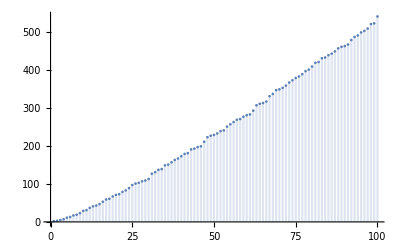

```mathematica
DiscretePlot[Prime[n],{n,1,100}]
```

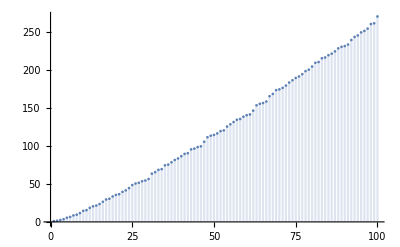

```mathematica
DiscretePlot[Prime[n]/2,{n,1,100}]
```

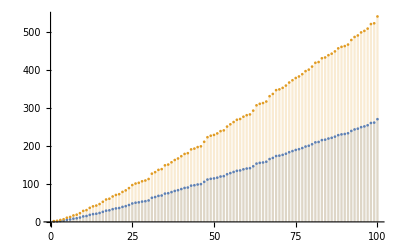

```mathematica
DiscretePlot[{Prime[n]/2,Prime[n]},{n,1,100}]
```

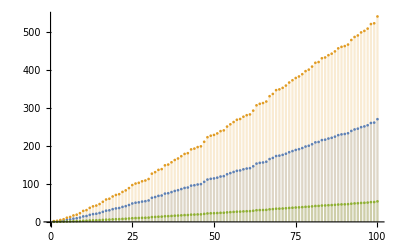

```mathematica
DiscretePlot[{Prime[n]/2,Prime[n],Prime[n]/10},{n,1,100}]
```

```mathematica
x∈∧x>0
```

x∈ℤ&&x>0&&x>0

```mathematica
Reduce[x∈Integers&&x>0&&x>0]
```

x∈ℤ&&x≥1

```mathematica
x∈∧x∈
```

x∈ℤ&&x>0&&x∈ℝ&&x>0

```mathematica
Reduce[x∈Integers&&x>0&&x∈Reals&&x>0]
```

x∈ℤ&&x≥1

```mathematica
IntegerDigits[543]
```

{5,4,3}

```mathematica
Table[IntegerDigits[543][[i]] 10^(i-1),{i,1,3}]
```

{5,40,300}

```mathematica
Table[Reverse@IntegerDigits[543][[i]] 10^(i-1),{i,1,3}]
```

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[5].

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[4].

Reverse::normal: Nonatomic expression expected at position 1 in Reverse[3].

General::stop: Further output of Reverse::normal will be suppressed during this calculation.

{Reverse[5],10 Reverse[4],100 Reverse[3]}

```mathematica
Table[Reverse[IntegerDigits[543]][[i]] 10^(i-1),{i,1,3}]
```

{3,40,500}

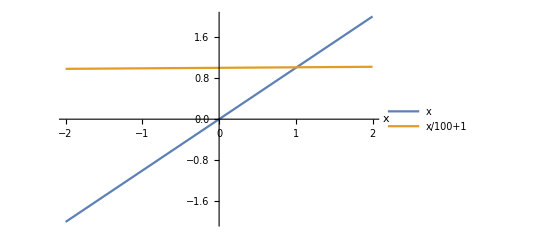

```mathematica
Plot[{x,x/100+1},{x,-2,2},PlotRange->Full,AxesLabel->Automatic,PlotLegends->"Expressions"]
```

```mathematica
Solve[x==x/100+1,x,Reals]
```

{{x→100/99}}

```mathematica
Normalize[a].Normalize[b]==c
```

Normalize[a].Normalize[b]==c

```mathematica
Normalize[{1,2}].Normalize[{2,3}]==c
```

8/(√65)==c

```mathematica
Normalize[{1,2}].Normalize[{x,f[x]}]==c
```

x/(√5 √(Abs[x]^2+Abs[f[x]]^2))+(2 f[x])/(√5 √(Abs[x]^2+Abs[f[x]]^2))==c

```mathematica
FullSimplify[x/(√5 √(Abs[x]^2+Abs[f[x]]^2))+(2 f[x])/(√5 √(Abs[x]^2+Abs[f[x]]^2))==c,{c,x,f[x]}∈Reals]
```

(x+2 f[x])/(√5 √(x^2+f[x]^2))==c

```mathematica
ExpandAll[(x+2 f[x])/(√5 √(x^2+f[x]^2))]==c
```

x/(√5 √(x^2+f[x]^2))+(2 f[x])/(√5 √(x^2+f[x]^2))==c

```mathematica
Grad[(x^3-x)-λ (x^3-x),{x,y,λ}]
```

{-1+3 x^2-(-1+3 x^2) λ,0,x-x^3}

```mathematica
Map[#==0&,{-1+3 x^2-(-1+3 x^2) λ,0,x-x^3}]
```

{-1+3 x^2-(-1+3 x^2) λ==0,True,x-x^3==0}

```mathematica
Solve[{-1+3 x^2-(-1+3 x^2) λ==0,True,x-x^3==0},x]
```

{}

```mathematica
Grad[(x^3-x)-λ (x^3-x),{x,λ}]
```

{-1+3 x^2-(-1+3 x^2) λ,x-x^3}

```mathematica
Map[#==0&,{-1+3 x^2-(-1+3 x^2) λ,x-x^3}]
```

{-1+3 x^2-(-1+3 x^2) λ==0,x-x^3==0}

```mathematica
Solve[{-1+3 x^2-(-1+3 x^2) λ==0,x-x^3==0},x]
```

{}

```mathematica
Solve[-1+3 x^2-(-1+3 x^2) λ==0,x]
```

{{x→-1/(√3)},{x→1/(√3)}}

```mathematica
f[x]==x^3-x
```

f[x]==-x+x^3

```mathematica
Map[f[x]==x^3-x/.#&,{{x->-1/(√3)},{x->1/(√3)}}]
```

{f[-1/(√3)]==2/(3 √3),f[1/(√3)]==-2/(3 √3)}

```mathematica
D[f[x]==x^3-x,x]
```

f'[x]==-1+3 x^2

```mathematica
Map[f'[x]==-1+3 (x^2).#&,{{x->-1/(√3)},{x->1/(√3)}}]
```

{f'[x]==-1+3 x^2.{x→-1/(√3)},f'[x]==-1+3 x^2.{x→1/(√3)}}

```mathematica
Map[f'[x]==-1+3 x^2/.#&,{{x->-1/(√3)},{x->1/(√3)}}]
```

{f'[-1/(√3)]==0,f'[1/(√3)]==0}

```mathematica
ExpandAll[(x^3-x)-λ (x^3-x)]
```

-x+x^3+x λ-x^3 λ

```mathematica
D[(x^3-x)-λ(3 x^2-1),x]==0
```

-1+3 x^2-6 x λ==0

```mathematica
Solve[-1+3 x^2-6 x λ==0,x]
```

{{x→1/3 (3 λ-√3 √(1+3 λ^2))},{x→1/3 (3 λ+√3 √(1+3 λ^2))}}

```mathematica
D[(x^3-x)-λ (x^3-x),x]==0
```

-1+3 x^2-(-1+3 x^2) λ==0

```mathematica
Solve[-1+3 x^2-(-1+3 x^2) λ==0,{x}]
```

{{x→-1/(√3)},{x→1/(√3)}}

```mathematica
Solve[-1+3 x^2-(-1+3 x^2) λ==0,λ]
```

{{λ→1}}

```mathematica
D[(x^3-x)-λ (3 x^2-1),x]==0
```

-1+3 x^2-6 x λ==0

```mathematica
Solve[-1+3 x^2-6 x λ==0,{x}]
```

{{x→1/3 (3 λ-√3 √(1+3 λ^2))},{x→1/3 (3 λ+√3 √(1+3 λ^2))}}

```mathematica
D[x^3-x,x]
```

-1+3 x^2

```mathematica
Map[-1+3 x^2==0/.#&,Out[121]]
```

{-1+1/3 (3 λ-√3 √(1+3 λ^2))^2==0,-1+1/3 (3 λ+√3 √(1+3 λ^2))^2==0}

```mathematica
Reduce[{-1+1/3 (3 λ-√3 √(1+3 λ^2))^2==0,-1+1/3 (3 λ+√3 √(1+3 λ^2))^2==0}]
```

λ==0

```mathematica
FullSimplify[{-1+1/3 (3 λ-√3 √(1+3 λ^2))^2==0,-1+1/3 (3 λ+√3 √(1+3 λ^2))^2==0},{x,λ}∈Reals]
```

{λ==0,λ==0}

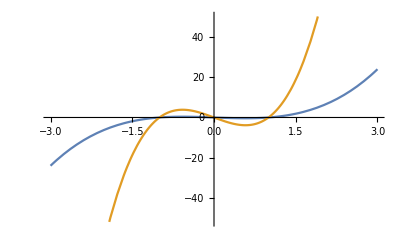

```mathematica
Plot[{x^3-x,10(x^3-x)},{x,-3,3}]
```